# Hard X-Rays Tracing

## 2 - Dimensional Case

```mathematica
Experimental data
```

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
files=FileNames[{"*.txt","*.txt_psd"},NotebookDirectory[]];
PSD1Dinit= Import[#,"Table"]&[Part[Select[#,StringEndsQ[#,"80x80um.txt_psd"]&]&@files,1]];
SurfaceVal=-0.049Import[#,"Table"][[17;;]]&@Part[Select[#,StringEndsQ[#,"80x80um.txt"]&]&@files,1];(*nm*)
Surfacepts:=Transpose[{ 10^3 Range[0,80,80/511],SurfaceVal[[#]]}]&(*nm*)
SurfaceFunc= Interpolation[Surfacepts[1], Method-> "Spline"];
σ=Mean[RootMeanSquare[SurfaceVal]];
```

```mathematica
PSD-function
```

```mathematica
PSD1D=Mean[80/512 Abs[Fourier[ SurfaceVal[[#]] 10^-3]//Drop[#,-Length[#]/2]&]^2&/@Range[512]];
PSD1Dfunc=GeneralizedLinearModelFit[{Range[1/80,511/80,1/40],PSD1D}//Transpose,{1,x,x^2,x^3},x,ExponentialFamily->"Gamma"];(*μm^3*)
```

```mathematica
Dielectric Permittivity
```

```mathematica
IndexRefr =Drop[Import[FileNames["*Al2O3.txt",NotebookDirectory[]][[1]],"Table"],2];
δ = Interpolation[IndexRefr[[All,{1,2}]],Method-> "Spline"];
γ = Interpolation[IndexRefr[[All,{1,3}]],Method-> "Spline"];
ε[λ_]:=1-δ[λ](*λ [nm]*)
εε[λ_]:=1-δ[λ]+ⅈ γ[λ](*λ [nm]*)
```

```mathematica
The Scattering Indicatrix
```

```mathematica
k=(2π)/#&;
t=(2 Sin[#])/(Sin[#]+√(ε[#2]-Cos[#]^2))&;
Π[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16π Sin[θ0] √(Cos[θ0]Cos[θ]))10^9 PSD1Dfunc[1/(λ 10^-3)Abs[Cos[θ0]-Cos[θ]]]
λ0 = 0.162;(*nm*)
θ0 = Abs[1-ε[λ0]]^(1/2);
AΠ[θinc_,λ_]:=AΠ[θinc,λ]=NIntegrate[Π[θ,θinc,λ],{θ,0,θ0,θinc,π/2}]
P[θ_,θ0_,λ_]:=Π[θ,θ0,λ]/AΠ[θ0,λ]
```

```mathematica
The Fresnel's Equations
```

```mathematica
Rf:=Abs[Cos[#+ArcSin[Cos[#]/√εε[#2]]]/Cos[#-ArcSin[Cos[#]/√εε[#2]]]]^2&
```

```mathematica
Total Integrated Scattering
```

```mathematica
TIS[θ0_,λ_,h_:1]:=Rf[θ0,λ](1-Exp[-((4π h σ Sin[θ0])/λ)^2])
Rs[θ0_,λ_,h_:1]:=Rf[θ0,λ]Exp[-((4π h σ Sin[θ0])/λ)^2]
```

```mathematica
PSD model
```

```mathematica
PSD1Dm=NonlinearModelFit[{Range[1/80,511/80,1/40],PSD1D}//Transpose,2/(√π)Gamma[1/2+αα]/Gamma[αα](σ^2 ξξ 10^-6)/((1+x^2 ξξ^2)^(1/2+αα)),{αα,ξξ},x];
{α,ξ}={αα,ξξ}/.PSD1Dm["BestFitParameters"];
Πm[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16π Sin[θ0] √(Cos[θ0]Cos[θ]))10^9 PSD1Dm[1/(λ 10^-3)Abs[Cos[θ0]-Cos[θ]]]
AΠm[θinc_,λ_]:=AΠm[θinc,λ]=NIntegrate[Πm[θ,θinc,λ],{θ,0,θ0,θinc,π/2}]
Pm[θ_,θ0_,λ_]:=Πm[θ,θ0,λ]/AΠm[θ0,λ]
σ=Mean[RootMeanSquare[SurfaceVal]];
```

```mathematica
Random Number Generator
```

```mathematica
RNG[y_,N_Integer]:=RandomVariate[ProbabilityDistribution[Π[x,y,λ0],{x,0,89°},Assumptions->0<y<89°,Method->"Normalize"],N]
RNGm[y_,N_Integer]:=RandomVariate[ProbabilityDistribution[Πm[x,y,λ0],{x,0,89°},Assumptions->0<y<89°,Method->"Normalize"],N]
```

```mathematica
The Experiment Geometry
```

```mathematica
r=20000 ;(*mirror radius of curvature [mm]*)
d = 250;(*mirror diameter [mm]*)
l1=400;(*distance between source and mirror [mm]*)
l2=185;(*distance between mirror and detector [mm]*)
ψ=2.ArcSin[d/(2r)];(*mirror apex angle*)
dmax=r θ0^2/2;
```

```mathematica
(*x - longitudinal coordinate, y - transverse coordinate*)
(*linepar = {z, y coordinates of source point, altitude θ of incidence}*)
InitLine2D:={-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2)+RandomReal[{0,dmax}],-ψ/2}
InitLine2D2:={-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2),RandomReal[{-ψ/2,ArcTan[-(Tan[ψ/2](l1-d/2))/l1]}]}
Δ:=√((#[[1]]Cos[#[[3]]]+(#[[2]]-r)Sin[#[[3]]])^2-(#[[1]])^2-(#[[2]])^2+2r#[[2]])&
Intersect:=
{{x->#[[1]]+Cos[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]-Δ@#),
y->#[[2]]+Sin[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]-Δ@#)},
{x->#[[1]]+Cos[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]+Δ@#),
y->#[[2]]+Sin[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]+Δ@#)}}&
CirCross:=MaximalBy[Select[Intersect@#,-π/2-ψ/2≤(ArcTan[x,y-r]/.#)≤-π/2+ψ/2&],x/.#&][[1]]&
DetCoord:={l2,#[[2]]+(l2-#[[1]])Tan[#[[3]]]}&
IncVec:={Cos[#[[3]]],Sin[#[[3]]]}&
IncAng:=Abs[π/2-VectorAngle[IncVec@#,{x,y-r}/.CirCross@#]]&
SpecVec:=IncVec@#-2(Normalize[{x,y-r}/.CirCross@#].IncVec@#)Normalize[{x,y-r}/.CirCross@#]&
ScVec:=RotationMatrix[RNG[IncAng@#,1][[1]]].(IncVec@#-(Normalize[{x,y-r}/.CirCross@#].IncVec@#)Normalize[{x,y-r}/.CirCross@#])&
```

```mathematica
Ray Tracing Demonstration
```

```mathematica
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#∈Reals,
{NestWhileList[(If[sw<TIS[IncAng@#,λ0],{x,y,ArcTan[#1,#2]&@@ScVec@#}/.CirCross@#,
{x,y,ArcTan[#1,#2]&@@SpecVec@#}/.CirCross@#])&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y}/.CirCross@#1,10]≠SetPrecision[{x,y}/.CirCross@#2,10] )&,2],fl},{{#},0}
]
]&
TracePlot[trace_,opts:OptionsPattern[]]:=If[trace[[2]]==1,Show[ParametricPlot[{r Cos[θ],r Sin[θ]+r},{θ,-π/2-ψ/2,-π/2+ψ/2}],Graphics[{Green,Opacity[0.6],PointSize[Medium],Point[{x,y}/.CirCross@#]&/@trace[[1]]}],Graphics[{Thick,Red,Opacity[0.4],Line[Append[Prepend[{x,y}/.CirCross[#]&/@trace[[1]],First[trace[[1]]][[1;;2]]],DetCoord[Last[trace[[1]]]]]]}],Evaluate[FilterRules[{opts},Options[Plot]]]],
Show[ParametricPlot[{r Cos[θ],r Sin[θ]+r},{θ,-π/2-ψ/2,-π/2+ψ/2}],Graphics[{Green,Opacity[0.6],PointSize[Medium],Point[{x,y}/.CirCross@#]&/@trace[[1]]}],Graphics[{Thick,Red,Opacity[0.4],Line[Prepend[{x,y}/.CirCross[#]&/@trace[[1]],First[trace[[1]]][[1;;2]]]]}],Evaluate[FilterRules[{opts},Options[Plot]]]]]
```

```mathematica
Ray Tracing Core
```

```mathematica
RayTracing2D[len_,OptionsPattern[{"PlaneWave"->True,"IncAngle"->0,"RMSHeight"->σ,"Precision"->MachinePrecision,"Monitoring"->True,"N"->10}]]:=Block[{SurfaceVal,PSD1D,PSD1Dfunc,Π,TIS,RNG,InitLine2D,Δ,CirCross,IncAng,IncVec,SpecVec,ScVec,trace,partable,j},
SurfaceVal=-0.049(OptionValue["RMSHeight"]/σ) Import[#,"Table"][[17;;]]&@Part[Select[#,StringEndsQ[#,"80x80um.txt"]&]&@files,1];
PSD1D=Mean[80/512 Abs[Fourier[ SurfaceVal[[#]] 10^-3]//Drop[#,-Length[#]/2]&]^2&/@Range[512]];
PSD1Dfunc=GeneralizedLinearModelFit[{Range[1/80,511/80,1/40],PSD1D}//Transpose,{1,x,x^2,x^3},x,ExponentialFamily->"Gamma"];
Π[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16π Sin[θ0] √(Cos[θ0]Cos[θ]))10^9 PSD1Dfunc[1/(λ 10^-3)Abs[Cos[θ0]-Cos[θ]]];
TIS[θ0_,λ_]:=Rf[θ0,λ](1-Exp[-((4π OptionValue["RMSHeight"] Sin[θ0])/λ)^2]);
RNG[y_,N_Integer]:=RandomVariate[ProbabilityDistribution[Π[x,y,λ0],{x,0,89°},Assumptions->0<y<89°,Method->"Normalize"],N,WorkingPrecision->OptionValue["Precision"]];
If[OptionValue["PlaneWave"],
InitLine2D:={-l1,r-Cot[ψ/2]d/2+Tan[ψ/2+OptionValue["IncAngle"]](l1-d/2)+RandomReal[{0,dmax},WorkingPrecision->OptionValue["Precision"]],-ψ/2+OptionValue["IncAngle"]},
InitLine2D:={-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2),RandomReal[{-ψ/2,ArcTan[-(Tan[ψ/2](l1-d/2))/l1]},WorkingPrecision->OptionValue["Precision"]]}
];
Δ:=√((#[[1]]Cos[#[[3]]]+(#[[2]]-r)Sin[#[[3]]])^2-(#[[1]])^2-(#[[2]])^2+2r#[[2]])&;
CirCross:=MaximalBy[Select[{{x->#[[1]]+Cos[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]-Δ@#),
y->#[[2]]+Sin[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]-Δ@#)},
{x->#[[1]]+Cos[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]+Δ@#),
y->#[[2]]+Sin[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]+Δ@#)}}&@#,-π/2-ψ/2≤(ArcTan[x,y-r]/.#)≤-π/2+ψ/2&],x/.#&][[1]]&;
IncAng:=Abs[π/2-VectorAngle[{Cos[#[[3]]],Sin[#[[3]]]}&@#,{x,y-r}/.CirCross@#]]&;
IncVec:={Cos[#[[3]]],Sin[#[[3]]]}&;
SpecVec:=IncVec@#-2(Normalize[{x,y-r}/.CirCross@#].IncVec@#)Normalize[{x,y-r}/.CirCross@#]&;
ScVec:=RotationMatrix[RNG[IncAng@#,1][[1]]].(IncVec@#-(Normalize[{x,y-r}/.CirCross@#].IncVec@#)Normalize[{x,y-r}/.CirCross@#])&;
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#∈Reals,
{NestWhileList[(If[sw<TIS[IncAng@#,λ0],{x,y,ArcTan[#1,#2]&@@ScVec@#}/.CirCross@#,
{x,y,ArcTan[#1,#2]&@@SpecVec@#}/.CirCross@#])&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y}/.CirCross@#1,10]≠SetPrecision[{x,y}/.CirCross@#2,10] )&,2],fl},{{#},0}]]&;
j=0;
partable=If[OptionValue["Monitoring"],
AbsoluteTiming[Select[Monitor[Flatten[Table[j++;ParallelTable[trace@InitLine2D,{i,1,len/OptionValue["N"]}],{i,1,OptionValue["N"]}],1],Row[{ProgressIndicator[j,{1,OptionValue["N"]}],ToString[100j/OptionValue["N"]]<>"%"}]],#[[2]]==1&]],
AbsoluteTiming[Select[ParallelTable[trace@InitLine2D,{i,1,len}],#[[2]]==1&]],
"BadOptionValue"];
partable[[1]]="curvature = "<>ToString[IntegerPart[r]]<>" mm, diameter = "<>ToString[IntegerPart[d]]<>" mm, rays = "<>ToString[len]<>", transmitted rays = "<>ToString[Length[partable[[2]]]]<>", time = "<>ToString[partable[[1]]]<>" s, plane wave = "<>ToString[OptionValue["PlaneWave"]]<>"\n";
partable
]
```

```mathematica
(*------------------------------------------*)
RayTracing2Dm[len_,OptionsPattern[{"PlaneWave"->True,"IncAngle"->0,"RMSHeight"->σ,"CorrLength"->ξ,"Precision"->MachinePrecision,"Monitoring"->True,"N"->10}]]:=Block[{PSD1Dm,Π,TIS,RNG,InitLine2D,Δ,CirCross,IncAng,IncVec,SpecVec,ScVec,trace,partable,j},
PSD1Dm[p_]:=2./(√π)Gamma[1./2+α]/Gamma[α](OptionValue["RMSHeight"]^2 OptionValue["CorrLength"] 10^-6)/((1+p^2 ξ^2)^(1/2+α));

Π[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16π Sin[θ0] √(Cos[θ0]Cos[θ]))10^9 PSD1Dm[1/(λ 10^-3)Abs[Cos[θ0]-Cos[θ]]];
TIS[θ0_,λ_]:=Rf[θ0,λ](1-Exp[-((4π OptionValue["RMSHeight"] Sin[θ0])/λ)^2]);
RNG[y_,N_Integer]:=RandomVariate[ProbabilityDistribution[Π[x,y,λ0],{x,0,89°},Assumptions->0<y<89°,Method->"Normalize"],N,WorkingPrecision->OptionValue["Precision"]];
If[OptionValue["PlaneWave"],
InitLine2D:={-l1,r-Cot[ψ/2]d/2+Tan[ψ/2+OptionValue["IncAngle"]](l1-d/2)+RandomReal[{0,dmax},WorkingPrecision->OptionValue["Precision"]],-ψ/2+OptionValue["IncAngle"]},
InitLine2D:={-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2),RandomReal[{-ψ/2,ArcTan[-(Tan[ψ/2](l1-d/2))/l1]},WorkingPrecision->OptionValue["Precision"]]}
];
Δ:=√((#[[1]]Cos[#[[3]]]+(#[[2]]-r)Sin[#[[3]]])^2-(#[[1]])^2-(#[[2]])^2+2r#[[2]])&;
CirCross:=MaximalBy[Select[{{x->#[[1]]+Cos[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]-Δ@#),
y->#[[2]]+Sin[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]-Δ@#)},
{x->#[[1]]+Cos[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]+Δ@#),
y->#[[2]]+Sin[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]+Δ@#)}}&@#,-π/2-ψ/2≤(ArcTan[x,y-r]/.#)≤-π/2+ψ/2&],x/.#&][[1]]&;
IncAng:=Abs[π/2-VectorAngle[{Cos[#[[3]]],Sin[#[[3]]]}&@#,{x,y-r}/.CirCross@#]]&;IncVec:={Cos[#[[3]]],Sin[#[[3]]]}&;
SpecVec:=IncVec@#-2(Normalize[{x,y-r}/.CirCross@#].IncVec@#)Normalize[{x,y-r}/.CirCross@#]&;
ScVec:=RotationMatrix[RNG[IncAng@#,1][[1]]].({Cos[#[[3]]],Sin[#[[3]]]}&@#-(Normalize[{x,y-r}/.CirCross@#].{Cos[#[[3]]],Sin[#[[3]]]}&@#)Normalize[{x,y-r}/.CirCross@#])&;
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#∈Reals,
{NestWhileList[(If[sw<TIS[IncAng@#,λ0],{x,y,ArcTan[#1,#2]&@@ScVec@#}/.CirCross@#,
{x,y,ArcTan[#1,#2]&@@SpecVec@#}/.CirCross@#])&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y}/.CirCross@#1,10]≠SetPrecision[{x,y}/.CirCross@#2,10] )&,2],fl},{{#},0}]]&;
j=0;
partable=If[OptionValue["Monitoring"],
AbsoluteTiming[Select[Monitor[Flatten[Table[j++;ParallelTable[trace@InitLine2D,{i,1,len/OptionValue["N"]}],{i,1,OptionValue["N"]}],1],Row[{ProgressIndicator[j,{1,OptionValue["N"]}],ToString[100j/OptionValue["N"]]<>"%"}]],#[[2]]==1&]],
AbsoluteTiming[Select[ParallelTable[trace@InitLine2D,{i,1,len}],#[[2]]==1&]],
"BadOptionValue"];
partable[[1]]="curvature = "<>ToString[IntegerPart[r]]<>" mm, diameter = "<>ToString[IntegerPart[d]]<>" mm, rays = "<>ToString[len]<>", transmitted rays = "<>ToString[Length[partable[[2]]]]<>", time = "<>ToString[partable[[1]]]<>" s, plane wave = "<>ToString[OptionValue["PlaneWave"]]<>"\n";
partable
]
```

```mathematica
Ray Tracing Standalone
```

```mathematica
Clear["Global`*"]
(*experiment geometry*)
r=20000 ;(*mirror radius of curvature [mm]*)
d = 250;(*mirror diameter [mm]*)
l1=400;(*distance between source and mirror [mm]*)
l2=185;(*distance between mirror and detector [mm]*)
ψ=2.ArcSin[d/(2r)];(*mirror apex angle*)
λ0 = 0.162;(*nm*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
files=FileNames[{"*.txt","*.txt_psd"},NotebookDirectory[]];
SurfaceVal=-0.049Import[#,"Table"][[17;;]]&@Part[Select[#,StringEndsQ[#,"80x80um.txt"]&]&@files,1];
σ=Mean[RootMeanSquare[SurfaceVal]];
PSD1D=Mean[80./512 Abs[Fourier[ SurfaceVal[[#]] 10^-3]//Drop[#,-Length[#]/2]&]^2&/@Range[512]];
PSD1Dm=NonlinearModelFit[{Range[1./80,511./80,1./40],PSD1D}//Transpose,2/(√π)Gamma[1/2+αα]/Gamma[αα](σ^2 ξξ 10^-6)/((1+x^2 ξξ^2)^(1/2+αα)),{αα,ξξ},x];
{α,ξ}={αα,ξξ}/.PSD1Dm["BestFitParameters"];
```

```mathematica
RayTracing[len_,OptionsPattern[{"PlaneWave"->True,"IncAngle"->0,"RMSHeight"->σ,"CorrLength"->ξ,"Precision"->MachinePrecision,"Monitoring"->True,"N"->10}]]:=Block[{IndexRefr,δ,γ,ε,εε,θ0,dmax,Rf,PSD1Dm,k,t,Π,TIS,RNG,InitLine2D,Δ,CirCross,IncAng,IncVec,SpecVec,ScVec,trace,j,partable},
IndexRefr = Drop[Import[#,"Table"],2]&[Part[Select[#,StringEndsQ[#,"Index of Refraction.txt"]&]&@files,1]];
δ = Interpolation[{IndexRefr[[All,1]],IndexRefr[[All,2]]}//Transpose,Method-> "Spline"];
γ = Interpolation[{IndexRefr[[All,1]],IndexRefr[[All,3]]}//Transpose,Method-> "Spline"];
ε[λ_]:=1.-δ[λ];
εε[λ_]:=1.-δ[λ]+ⅈ γ[λ];
θ0 = Abs[1-ε[λ0]]^(1/2);
dmax=r θ0^2/2;

Rf:=Abs[Cos[#+ArcSin[Cos[#]/√εε[#2]]]/Cos[#-ArcSin[Cos[#]/√εε[#2]]]]^2&;
PSD1Dm[p_]:=2./(√π)Gamma[1./2+α]/Gamma[α](OptionValue["RMSHeight"]^2 OptionValue["CorrLength"] 10^-6)/((1+p^2 ξ^2)^(1/2+α));
k=(2.π)/#&;
t=(2. Sin[#])/(Sin[#]+√(ε[#2]-Cos[#]^2))&;
Π[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16π Sin[θ0] √(Cos[θ0]Cos[θ]))10^9 PSD1Dm[1/(λ 10^-3)Abs[Cos[θ0]-Cos[θ]]];
TIS[θ0_,λ_]:=Rf[θ0,λ](1-Exp[-((4π OptionValue["RMSHeight"] Sin[θ0])/λ)^2]);
RNG[y_,N_Integer]:=RandomVariate[ProbabilityDistribution[Π[x,y,λ0],{x,0,89°},Assumptions->0<y<89°,Method->"Normalize"],N,WorkingPrecision->OptionValue["Precision"]];
If[OptionValue["PlaneWave"],
InitLine2D:={-l1,r-Cot[ψ/2]d/2+Tan[ψ/2+OptionValue["IncAngle"]](l1-d/2)+RandomReal[{0,dmax},WorkingPrecision->OptionValue["Precision"]],-ψ/2+OptionValue["IncAngle"]},
InitLine2D:={-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2),RandomReal[{-ψ/2,ArcTan[-(Tan[ψ/2](l1-d/2))/l1]},WorkingPrecision->OptionValue["Precision"]]}
];
Δ:=√((#[[1]]Cos[#[[3]]]+(#[[2]]-r)Sin[#[[3]]])^2-(#[[1]])^2-(#[[2]])^2+2r#[[2]])&;
CirCross:=MaximalBy[Select[{{x->#[[1]]+Cos[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]-Δ@#),
y->#[[2]]+Sin[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]-Δ@#)},
{x->#[[1]]+Cos[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]+Δ@#),
y->#[[2]]+Sin[#[[3]]](-#[[1]]Cos[#[[3]]]-(#[[2]]-r)Sin[#[[3]]]+Δ@#)}}&@#,-π/2-ψ/2≤(ArcTan[x,y-r]/.#)≤-π/2+ψ/2&],x/.#&][[1]]&;
IncAng:=Abs[π/2-VectorAngle[{Cos[#[[3]]],Sin[#[[3]]]}&@#,{x,y-r}/.CirCross@#]]&;
IncVec:={Cos[#[[3]]],Sin[#[[3]]]}&;
SpecVec:=IncVec@#-2(Normalize[{x,y-r}/.CirCross@#].IncVec@#)Normalize[{x,y-r}/.CirCross@#]&;
ScVec:=RotationMatrix[RNG[IncAng@#,1][[1]]].(IncVec@#-(Normalize[{x,y-r}/.CirCross@#].IncVec@#)Normalize[{x,y-r}/.CirCross@#])&;
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#∈Reals,
{NestWhileList[(If[sw<TIS[IncAng@#,λ0],{x,y,ArcTan[#1,#2]&@@ScVec@#}/.CirCross@#,
{x,y,ArcTan[#1,#2]&@@SpecVec@#}/.CirCross@#])&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y}/.CirCross@#1,10]≠SetPrecision[{x,y}/.CirCross@#2,10] )&,2],fl},{{#},0}]]&;
j=0;
partable=If[OptionValue["Monitoring"],
AbsoluteTiming[Select[Monitor[Flatten[Table[j++;ParallelTable[trace@InitLine2D,{i,1,len/OptionValue["N"]}],{i,1,OptionValue["N"]}],1],Row[{ProgressIndicator[j,{1,OptionValue["N"]}],ToString[100j/OptionValue["N"]]<>"%"}]],#[[2]]==1&]],
AbsoluteTiming[Select[ParallelTable[trace@InitLine2D,{i,1,len}],#[[2]]==1&]],
"BadOptionValue"];
partable[[1]]="curvature = "<>ToString[IntegerPart[r]]<>" mm, diameter = "<>ToString[IntegerPart[d]]<>" mm, rays = "<>ToString[len]<>", transmitted rays = "<>ToString[Length[partable[[2]]]]<>", time = "<>ToString[partable[[1]]]<>" s, plane wave = "<>ToString[OptionValue["PlaneWave"]]<>"\n";
partable
]
```

```mathematica
Calculation Results
```

```mathematica
SetDirectory[NotebookDirectory[]];
RayTracing[10^6,"N"->100]>>"2D_N10^6PLANE"
```

```mathematica
Results Demonstration
```

```mathematica
traces=<<"2D_N10^6PLANE";
detang=Last[#][[3]]&/@traces[[2,All,1]];
```

```mathematica
Results Processing
```

```mathematica
dα=1000. √(2dmax/r);
resultsξtable={results11,results16,results17,results12,results18,results13,results19,results14,results15};
resultsσtable={results5,results6,results7,results8,results9,results10};
ξtable={0.1,0.3,0.7,1,2,3,4.5,6,10};
dαξtable=2 √(2Log[2])Δ/.NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,150,0.17}],#[[1]]>dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x]["BestFitParameters"]&/@resultsξtable;
dαerror=10 √(2Log[2])NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,150,0.17}],#[[1]]>dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x]["ParameterErrors"][[2]]&/@resultsξtable;
dαξlefttable=2 √(2Log[2])Abs[Δ]/.NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000],#[[1]]<-dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x]["BestFitParameters"]&/@resultsξtable;
hξtable=c/.NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,50,0.17}],#[[1]]<-dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x]["BestFitParameters"]&/@resultsξtable;
dασtable=2 √(2Log[2])Δ/.NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,50,0.17}],#[[1]]>dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x]["BestFitParameters"]&/@resultsσtable;
hσtable=c/.NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,50,0.17}],#[[1]]<-dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x]["BestFitParameters"]&/@resultsσtable;
herror=4NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,50,0.17}],#[[1]]<-dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x]["ParameterErrors"][[1]]&/@resultsσtable;
Reffξtable=(Length/@resultsξtable)/10000.;
Reffσtable=(Length/@resultsσtable)/10000.;
```

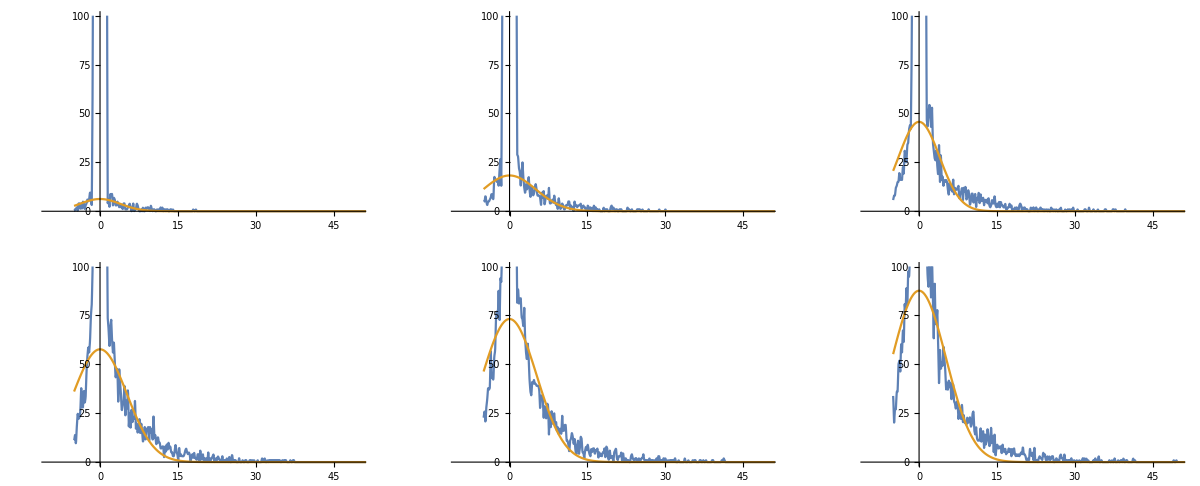

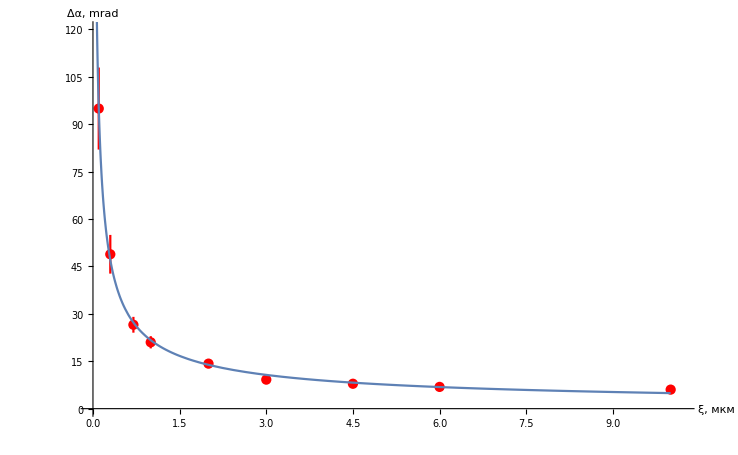

| Estimate | Standard Error | t-Statistic | P-Value
c | 21.6629 | 0.468369 | 46.2519 | 5.77368×10^-10
m | 0.643884 | 0.0107753 | 59.7554 | 9.6491×10^-11

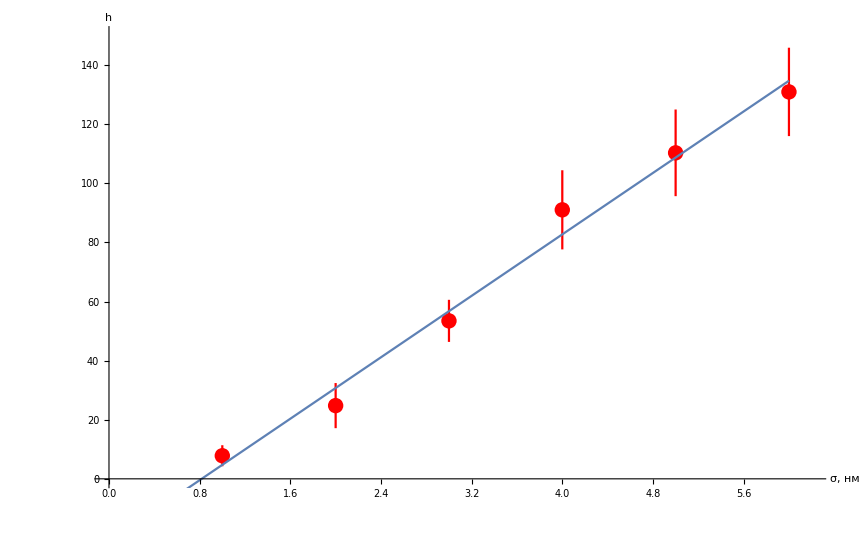

| Estimate | Standard Error | t-Statistic | P-Value
c | 25.9912 | 1.42134 | 18.2864 | 0.0000526055
a | -21.2559 | 5.53533 | -3.84004 | 0.0184589

```mathematica
Needs["ErrorBarPlots`"]
Interpolation[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(results6[[All,3]]-ψ/2)1000],InterpolationOrder->1];
NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(results6[[All,3]]-ψ/2)1000],#[[1]]>dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x];
GraphicsGrid[Partition[Plot[{Interpolation[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,50,0.17}],InterpolationOrder->1][y],NonlinearModelFit[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[(#[[All,3]]-ψ/2)1000,{-10,50,0.17}],#[[1]]>dα&],c Exp[-x^2/(2 Δ^2)],{c,Δ},x][y]}//Evaluate,{y,-5,150},PlotRange->{{-10,50},{0,100}}]&/@resultsσtable,3],ImageSize->Full]
Show[ErrorListPlot[Table[{{ξtable[[i]],dαξtable[[i]]},ErrorBar[dαerror[[i]]]},{i,1,Length[ξtable]}],PlotStyle->{Red,PointSize[0.01]}],Plot[NonlinearModelFit[{ξtable,dαξtable}//Transpose,c/x^m,{c,m},x][y],{y,0,10},PlotRange->All],ImageSize->Medium,AxesStyle->15,AxesLabel->{Style["ξ, мкм",15,Gray],Style["Δα, mrad",15,Gray]},PlotRange->{{0,10.2},{0,120}} ]
NonlinearModelFit[{ξtable,dαξtable}//Transpose,c/x^m,{c,m},x]["ParameterTable"]
Show[ErrorListPlot[{hσtable,herror}//Transpose,ImageSize->Medium,PlotStyle->Red],Plot[NonlinearModelFit[{Range[6],hσtable}//Transpose,c x+a,{c,a},x][y],{y,0,6}],AxesStyle->15,AxesLabel->{Style["σ, нм",15,Gray],Style["h",15,Gray]},PlotRange->{{0,6.2},{0,150}}]
NonlinearModelFit[{Range[6],hσtable}//Transpose,c x+a,{c,a},x]["ParameterTable"]
```

## 3 - Dimensional Case

```mathematica
Initialization
```

```mathematica
(*Clear["Global`*"]*)
SetDirectory[NotebookDirectory[]];
files=FileNames[{"*.txt","*.txt_psd"},NotebookDirectory[]];
SurfaceVal=-0.049Import[#,"Table"][[17;;]]&@Part[Select[#,StringEndsQ[#,"80x80um.txt"]&]&@files,1];
σ=Mean[RootMeanSquare[SurfaceVal]];
PSD1D=Mean[80./512 Abs[Fourier[ SurfaceVal[[#]] 10^-3]//Drop[#,-Length[#]/2]&]^2&/@Range[512]];
PSD1Dm=NonlinearModelFit[{Range[1./80,511./80,1./40],PSD1D}//Transpose,2/(√π)Gamma[1/2+αα]/Gamma[αα](σ^2 ξξ 10^-6)/((1+x^2 ξξ^2)^(1/2+αα)),{αα,ξξ},x];
{α,ξ}={αα,ξξ}/.PSD1Dm["BestFitParameters"];
IndexRefr = Drop[Import[FileNames["*Al2O3.txt",NotebookDirectory[]][[1]],"Table"],2];
δ = Interpolation[IndexRefr[[All,{1,2}]],Method-> "Spline"];
γ = Interpolation[IndexRefr[[All,{1,3}]],Method-> "Spline"];
ε[λ_]:=1-δ[λ](*λ [nm]*)
εε[λ_]:=1-δ[λ]+ⅈ γ[λ](*λ [nm]*)
λ0 = 0.162;(*nm*)
θ0 = Abs[1-ε[λ0]]^(1/2);
k=(2π)/#&;
t=(2 Sin[#])/(Sin[#]+√(ε[#2]-Cos[#]^2))&;
Rf:=Abs[Cos[#+ArcSin[Cos[#]/√εε[#2]]]/Cos[#-ArcSin[Cos[#]/√εε[#2]]]]^2&
TIS[θ0_,λ_]:=Rf[θ0,λ](1-Exp[-((4π σ Sin[θ0])/λ)^2])
Rs[θ0_,λ_]:=Rf[θ0,λ]Exp[-((4π σ Sin[θ0])/λ)^2]
Πm[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16π Sin[θ0] √(Cos[θ0]Cos[θ]))10^9 PSD1Dm[1/(λ 10^-3)Abs[Cos[θ0]-Cos[θ]]]
mydistm[y_]:=ProbabilityDistribution[Πm[x,y,λ0],{x,0,π/2},Assumptions->0<y<π/2,Method->"Normalize"]
SetOptions[DensityHistogram,{ChartLegends->Automatic,ColorFunction->(Hue[0.7(1-#),1,0.85]&),ImageSize->Large}];
SetOptions[Plot3D,{BoxRatios->{1,1,1/3},PlotRange->{{-1.5d/2,1.5d/2},{-1.5d/2,1.5d/2},{0,3(r-Cot[ψ/2]d/2)}},ImageSize->Large,AxesLabel->{x,y,z}}];
```

```mathematica
2-Dimensional PSD-function
```

```mathematica
PSD2D=Mean[Mean[(80/512)^2 Abs[Fourier/@Partition[SurfaceVal 10^-3,{16,16}]//Drop[#,None,None,-Dimensions[#][[3]]/2,-Dimensions[#][[4]]/2]&]^2]];
PSD2Dfunc=GeneralizedLinearModelFit[Table[{Range[0,511/80,511/(80(Dimensions[PSD2D][[1]]-1))][[i]],Range[0,511/80,511/(80(Dimensions[PSD2D][[2]]-1))][[j]],PSD2D[[i,j]]},{i,1,Dimensions[PSD2D][[1]]},{j,1,Dimensions[PSD2D][[2]]}]//Flatten[#,1]&,{x,y,x^2,y^2,x^3,y^3,x^4,y^4,x^5,y^5,x y,x y^2,y x^2,x^2 y^2,x^3 y,x y^3,x^4 y,x^2 y^3,x^3 y^2,x y^4},{x,y},ExponentialFamily->"Binomial"];(*not appropriate*)
PSD2Dm:=(10^-6 σ^2 ξ^2 α)/(π(1+(#1^2+#2^2)ξ^2)^(1+α))&
```

```mathematica
2-Dimensional Scattering Indicatrix
```

```mathematica
Φ[θ_,φ_,θ0_,λ_]:=(k[λ]^4 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/((4π)^2 Sin[θ0](*√(Cos[θ0]Cos[θ])*))10^12 PSD2Dm[1/(λ 10^-3)(Cos[θ]Cos[φ]-Cos[θ0]),1/(λ 10^-3)Cos[θ]Sin[φ]]
AΦ[θinc_,λ_]:=AΦ[θinc,λ]=NIntegrate[Φ[θsc,φsc,θinc,λ]Cos[θsc],{θsc,0,θ0,θinc,π/2},{φsc,-π,π}]
F[θ_,φ_,θ0_,λ_]:=Φ[θ,φ,θ0,λ]/AΦ[θ0,λ]
```

```mathematica
Random Number Generator
```

```mathematica
mydist2[θsc_,θinc_]:=ProbabilityDistribution[Φ[θsc,x,θinc,λ0],{x,-π,π},Assumptions->0<θinc<π/2,Assumptions->0<θsc<π/2,Method->"Normalize"]
RNG[y_,len_,prec_:MachinePrecision]:=Quiet[Check[Module[{x1,x2},
x1=RandomVariate[mydistm[y],len,WorkingPrecision->prec];
x2=RandomVariate[mydist2[#,y],WorkingPrecision->prec]&/@x1;
Transpose[{x1,x2}]
],ConstantArray[{y,0},len],RandomVariate::noimp]]
```

## Tracing on a spherical surface

```mathematica
The Experiment Geometry
```

```mathematica
(*new experiment geometry*)
r=1000.;(*radius of curvature [mm]*)
d=60.;(*the mirror diameter [mm]*)
l1=195.;(*distance between the source and the mirror [mm]*)
l2=185.;(*distance between the mirror and the detector [mm]*)
L=100.;(*length of the source [mm]*)
ψ=2.ArcSin[d/(2r)];(*the mirror apex angle*)
dmax=r θ0^2/2;
α0=L^2/(16 l1^2)Sin[ψ]/(1-d/(2l1));
```

```mathematica
(*y - longitudinal coordinate; x - transverse coordinate; z - height*)
(*linepar = {x, y, z coordinates of source point, altitude θ, azimuth φ of incedence}*)
InitLine3D[α_:0]:=Module[{x0,φ0,θ0},
x0=RandomReal[{-L/2,L/2}];
φ0=π/2-RandomReal[{ArcTan[-x0/l1]-ArcSin[(d/2)/(√(l1^2+x0^2))],ArcTan[-x0/l1]+ArcSin[(d/2)/(√(l1^2+x0^2))]}];
θ0=RandomReal[{ArcTan[((l1-d/2) Tan[α+ψ/2])/(x0 Cos[φ0]-l1 Sin[φ0]+√(d^2/4-(x0 Sin[φ0]+l1 Cos[φ0])^2))],ArcTan[(( l1-d/2) Tan[α+ψ/2])/(x0 Cos[φ0]-l1 Sin[φ0]-√(d^2/4-(x0 Sin[φ0]+l1 Cos[φ0])^2))]}];
{x0,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2+α](l1-d/2),θ0,φ0}]
UniformDisk/:
Random`DistributionVector[UniformDisk[r_?Positive],n_Integer,prec_?Positive]:=
r*Sqrt[RandomReal[1,n,WorkingPrecision->prec]]*
Transpose[{Cos[#],Sin[#]}&[RandomReal[2Pi,n,WorkingPrecision->prec]]]
InitLine3D2[α_:0]:={#1,-l1,Tan[ψ/2+α](l1+#2)+r-Cot[ψ/2]d/2,-ψ/2-α,π/2.}&@@RandomVariate[UniformDisk[d/2]]
InitLineTest1:={0,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2),-ψ/2+#,π/2.}&
InitLineTest2:={0,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2)+#,-ψ/2,π/2.}&
Δ:=(#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧])^2-(#⟦1⟧)^2-(#⟦2⟧)^2-(#⟦3⟧)^2+2 r #⟦3⟧&
Intersect:=
{{x->#⟦1⟧-Cos[#⟦4⟧]Cos[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Sqrt[Δ@#]),
y->#⟦2⟧-Cos[#⟦4⟧]Sin[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Sqrt[Δ@#]),
z->#⟦3⟧-Sin[#⟦4⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Sqrt[Δ@#])},
{x->#⟦1⟧-Cos[#⟦4⟧]Cos[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Sqrt[Δ@#]),y->#⟦2⟧-Cos[#⟦4⟧]Sin[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Sqrt[Δ@#]),
z->#⟦3⟧-Sin[#⟦4⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Sqrt[Δ@#])}
}&
SphCross:=MaximalBy[Select[Intersect[#],π-ψ/2≤(ArcTan[z-r,√(x^2+y^2)]/.#)≤π&],y/.#&][[1]]&
IncVec:={Cos[#[[4]]]Cos[#[[5]]],Cos[#[[4]]]Sin[#[[5]]],Sin[#[[4]]]}&
IncAng:=Abs[π/2-VectorAngle[IncVec@#,{x,y,z-r}/.SphCross@#]]&
SpecVec:=IncVec@#-2(Normalize[{x,y,z-r}/.SphCross@#].IncVec@#)Normalize[{x,y,z-r}/.SphCross@#]&
ScVec:=RotationMatrix[RNG[IncAng@#,1][[1,2]],-{x,y,z-r}/.SphCross@#].RotationMatrix[RNG[IncAng@#,1][[1,1]],{{x,y,z-r}/.SphCross@#,IncVec@#-(Normalize[{x,y,z-r}/.SphCross@#].IncVec@#)Normalize[{x,y,z-r}/.SphCross@#]}].(IncVec@#-(Normalize[{x,y,z-r}/.SphCross@#].IncVec@#)Normalize[{x,y,z-r}/.SphCross@#])&
```

```mathematica
Show[ParametricPlot3D[{r Sin[θ]Cos[φ],r Sin[θ]Sin[φ],r(1+Cos[θ])},{θ,-π,-π+ψ/2},{φ,0,2π},PlotRange->All],Graphics3D[{Thick,Red,Line[{#[[1;;3]],{x,y,z}/.SphCross[#]}]}],Graphics3D[{Thick,Green,HalfLine[{x,y,z}/.SphCross[#],SpecVec@#]}],Graphics3D[{Green,PointSize[Large],Point[{x,y,z}/.SphCross[#]]}],BoxRatios->{1,1,1/3},PlotRange->{{-1.5d/2,1.5d/2},{-1.5d/2,1.5d/2},{0,3(r-Cot[ψ/2]d/2)}},ImageSize->Large,AxesLabel->{x,y,z}]&@InitLineTest2[Tan[ψ/2]d](*Red - incident; Green - Scattered*)
```

-Graphics3D-

```mathematica
Ray Tracing Demonstration
```

```mathematica
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#>10^-3,{NestWhileList[(If[sw<TIS[IncAng@#,λ0],{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@ScVec@#,ArcTan[#1,#2]&@@ScVec@#}/.SphCross@#,{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@SpecVec@#,ArcTan[#1,#2]&@@SpecVec@#}/.SphCross@#])&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y,z}/.SphCross@#1,10]≠ SetPrecision[{x,y,z}/.SphCross@#2,10])&,2],fl},{{#},0}]]&
DetCoord:={#[[1]]+l2 Cot[#[[5]]]-#[[2]] Cot[#[[5]]],l2,#[[3]]+l2 Csc[#[[5]]] Tan[#[[4]]]-#[[2]] Csc[#[[5]]] Tan[#[[4]]]}&
TracePlot[trace_,opts:OptionsPattern[]]:=Show[ParametricPlot3D[{r Sin[θ]Cos[φ],r Sin[θ]Sin[φ],r(1+Cos[θ])},{θ,-π,-π+ψ/2},{φ,0,2π}],ParametricPlot3D[{l2,t,s},{t,-200,200},{s,0,1},PlotStyle->{Gray,Opacity[0.5]}],Graphics3D[{Green,PointSize[Large],Point[#[[1;;3]]]}]&/@trace[[1]],
If[trace[[2]]==0,Graphics3D[Line[#[[1;;3]]&/@trace[[1]]]],Graphics3D[Line[Append[#[[1;;3]]&/@trace[[1]],DetCoord[Last@trace[[1]]]]]]],Evaluate[FilterRules[{opts},Options[Plot3D]]]]
ListTracePlot[mtrace_,opts:OptionsPattern[]]:=
Show[ParametricPlot3D[{r Sin[θ]Cos[φ],r Sin[θ]Sin[φ],r(1+Cos[θ])},{θ,-π,-π+ψ/2},{φ,0,2π}],ParametricPlot3D[{l2,t,s},{t,-200,200},{s,0,1},PlotStyle->{Gray,Opacity[0.5]}],
Graphics3D[Line[Append[#[[1;;3]]&/@#[[1]],DetCoord[Last@#[[1]]]]]]&/@mtrace[[2]],
Map[Graphics3D[{Green,PointSize[Large],Point[#[[1;;3]]]}]&,mtrace[[2,All,1]],{2}]//Flatten
,Evaluate[FilterRules[{opts},Options[Plot3D]]]]
```

```mathematica
TracePlot[trace@InitLineTest2[dmax/2],BoxRatios->{1,1,1/3},PlotRange->{{-1.5d/2,1.5d/2},{-1.5d/2,1.5d/2},{0,3(r-Cot[ψ/2]d/2)}},ImageSize->Large]
```

-Graphics3D-

```mathematica
Ray Tracing Core
```

```mathematica
RayTracing3D[len_,OptionsPattern[{"PlaneWave"->False,"IncAngle"->0,"RMSHeight"->σ,"CorrLength"->ξ,"Precision"->MachinePrecision,"Monitoring"->True,"Testing"->False,"N"->10}]]:=Block[{PSD1Dm,Π,PSD2Dm,Φ,TIS,mydist1,mydist2,RNG,InitLineTest,InitLine3D,Δ,SphCross,trace,partable,j},
PSD1Dm[p_]:=2./(√π)Gamma[1./2+α]/Gamma[α](OptionValue["RMSHeight"]^2 OptionValue["CorrLength"] 10^-6)/((1+p^2 ξ^2)^(1/2+α));

Π[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16π Sin[θ0] √(Cos[θ0]Cos[θ]))10^9 PSD1Dm[1/(λ 10^-3)Abs[Cos[θ0]-Cos[θ]]];
PSD2Dm:=(10^-6 OptionValue["RMSHeight"]^2 OptionValue["CorrLength"]^2 α)/(π(1.+(#1^2+#2^2)OptionValue["CorrLength"]^2)^(1+α))&;
Φ[θ_,φ_,θ0_,λ_]:=(k[λ]^4 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/((4π)^2 Sin[θ0])10^12 PSD2Dm[1/(λ 10^-3)(Cos[θ]Cos[φ]-Cos[θ0]),1/(λ 10^-3)Cos[θ]Sin[φ]];
TIS[θ0_,λ_]:=Rf[θ0,λ](1-Exp[-((4π  OptionValue["RMSHeight"]Sin[θ0])/λ)^2]);
mydist1[y_]:=ProbabilityDistribution[Π[x,y,λ0],{x,0,π/2},Assumptions->0<y<π/2,Method->"Normalize"];
mydist2[θsc_,θinc_]:=ProbabilityDistribution[Φ[θsc,x,θinc,λ0],{x,-π,π},Assumptions->0<θinc<π/2,Assumptions->0<θsc<π/2,Method->"Normalize"];
RNG[y_,length_]:=Quiet[Check[Block[{x1,x2},
x1=RandomVariate[mydist1[y],length,WorkingPrecision->OptionValue["Precision"]];
x2=RandomVariate[mydist2[#,y],WorkingPrecision->OptionValue["Precision"]]&/@x1;
Transpose[{x1,x2}]],ConstantArray[{y,0},len],RandomVariate::noimp]];
InitLineTest:={0,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2)+#,-ψ/2,π/2.}&;
If[OptionValue["PlaneWave"],
InitLine3D:={#1,-l1,Tan[ψ/2+OptionValue["IncAngle"]](l1+#2)+r-Cot[ψ/2]d/2,-ψ/2-OptionValue["IncAngle"],π/2.}&@@RandomVariate[UniformDisk[d/2],WorkingPrecision->OptionValue["Precision"]],
InitLine3D:=Module[{xinc,φinc,θinc},
xinc=RandomReal[{-L/2,L/2},WorkingPrecision->OptionValue["Precision"]];
φinc=π/2.-RandomReal[{ArcTan[-xinc/l1]-ArcSin[(d/2)/(√(l1^2+xinc^2))],ArcTan[-xinc/l1]+ArcSin[(d/2)/(√(l1^2+xinc^2))]},WorkingPrecision->OptionValue["Precision"]];
θinc=RandomReal[{ArcTan[((l1-d/2) Tan[OptionValue["IncAngle"]+ψ/2])/(xinc Cos[φinc]-l1 Sin[φinc]+√(d^2/4-(xinc Sin[φinc]+l1 Cos[φinc])^2))],ArcTan[(( l1-d/2) Tan[OptionValue["IncAngle"]+ψ/2])/(xinc Cos[φinc]-l1 Sin[φinc]-√(d^2/4-(xinc Sin[φinc]+l1 Cos[φinc])^2))]},WorkingPrecision->OptionValue["Precision"]];
{xinc,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2+OptionValue["IncAngle"]](l1-d/2),θinc,φinc}]];
Δ:=(#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧])^2-(#⟦1⟧)^2-(#⟦2⟧)^2-(#⟦3⟧)^2+2 r #⟦3⟧&;
SphCross:=MaximalBy[Select[
{{x->#⟦1⟧-Cos[#⟦4⟧]Cos[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Sqrt[Δ@#]),
y->#⟦2⟧-Cos[#⟦4⟧]Sin[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Sqrt[Δ@#]),
z->#⟦3⟧-Sin[#⟦4⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Sqrt[Δ@#])},
{x->#⟦1⟧-Cos[#⟦4⟧]Cos[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Sqrt[Δ@#]),y->#⟦2⟧-Cos[#⟦4⟧]Sin[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Sqrt[Δ@#]),
z->#⟦3⟧-Sin[#⟦4⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Sqrt[Δ@#])}},π-ψ/2≤(ArcTan[z-r,√(x^2+y^2)]/.#)≤π&],y/.#&][[1]]&;
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#∈Reals,{NestWhileList[(If[sw<TIS[IncAng@#,λ0],{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@ScVec@#,ArcTan[#1,#2]&@@ScVec@#}/.SphCross@#,{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@SpecVec@#,ArcTan[#1,#2]&@@SpecVec@#}/.SphCross@#])&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y,z}/.SphCross@#1,10]≠ SetPrecision[{x,y,z}/.SphCross@#2,10])&,2],fl},{{#},0}]]&;
j=0;
partable=If[OptionValue["Monitoring"],
If[OptionValue["Testing"],
AbsoluteTiming[Select[Monitor[Flatten[Table[j++;ParallelTable[trace@InitLineTest[dmax/2],{i,1,len/OptionValue["N"]}],{i,1,OptionValue["N"]}],1],Row[{ProgressIndicator[j,{1,OptionValue["N"]}],ToString[100j/OptionValue["N"]]<>"%"}]],#[[2]]==1&]],
AbsoluteTiming[Select[Monitor[Flatten[Table[j++;ParallelTable[trace@InitLine3D,{i,1,len/OptionValue["N"]}],{i,1,OptionValue["N"]}],1],Row[{ProgressIndicator[j,{1,OptionValue["N"]}],ToString[100j/OptionValue["N"]]<>"%"}]],#[[2]]==1&]],
"BadOptionValue"],
If[OptionValue["Testing"],
AbsoluteTiming[Select[ParallelTable[trace@InitLineTest[dmax/2],{i,1,len}],#[[2]]==1&]],
AbsoluteTiming[Select[ParallelTable[trace@InitLine3D,{i,1,len}],#[[2]]==1&]],
"BadOptionValue"],
"BadOptionValue"];
partable[[1]]="curvature = "<>ToString[IntegerPart[r]]<>" mm, diameter = "<>ToString[IntegerPart[d]]<>" mm, rays = "<>ToString[len]<>", transmitted rays = "<>ToString[Length[partable[[2]]]]<>", time = "<>ToString[partable[[1]]]<>" s, plane wave = "<>ToString[OptionValue["PlaneWave"]]<>"\n";
partable
]
```

## Tracing on a spherical surface with imperfections

### Custom imperfection shape approximation

```mathematica
The Experiment Geometry
```

```mathematica
(*new experiment geometry*)
r=1000.;(*radius of curvature [mm]*)
d=60.;(*the mirror diameter [mm]*)
l1=195.;(*distance between the source and the mirror [mm]*)
l2=185.;(*distance between the mirror and the detector [mm]*)
L=100.;(*length of the source [mm]*)
ψ=2.ArcSin[d/(2r)];(*the mirror apex angle*)
ζ=0.01; (*imperfection size [mm]*)
Nimp=1;(*number of imperfections*)
imploc=SortBy[{{-3.,0.},{0.,2.}},Last@#&];(*imperfections location*)
dmax=r θ0^2/2;
α0=L^2/(16 l1^2)Sin[ψ]/(1-d/(2l1));
```

```mathematica
(*y - longitudinal coordinate; x - transverse coordinate; z - height*)
(*linepar = {x, y, z coordinates of source point, altitude θ, azimuth φ of incedence}*)
InitLine3D[α_:0]:=Module[{x0,φ0,θ0},
x0=RandomReal[{-L/2,L/2}];
φ0=π/2-RandomReal[{ArcTan[-x0/l1]-ArcSin[(d/2)/(√(l1^2+x0^2))],ArcTan[-x0/l1]+ArcSin[(d/2)/(√(l1^2+x0^2))]}];
θ0=RandomReal[{ArcTan[((l1-d/2) Tan[α+ψ/2])/(x0 Cos[φ0]-l1 Sin[φ0]+√(d^2/4-(x0 Sin[φ0]+l1 Cos[φ0])^2))],ArcTan[(( l1-d/2) Tan[α+ψ/2])/(x0 Cos[φ0]-l1 Sin[φ0]-√(d^2/4-(x0 Sin[φ0]+l1 Cos[φ0])^2))]}];
{x0,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2+α](l1-d/2),θ0,φ0}]
UniformDisk/:
Random`DistributionVector[UniformDisk[r_?Positive],n_Integer,prec_?Positive]:=
r*Sqrt[RandomReal[1,n,WorkingPrecision->prec]]*
Transpose[{Cos[#],Sin[#]}&[RandomReal[2Pi,n,WorkingPrecision->prec]]]
InitLine3D2[α_:0]:={#1,-l1,Tan[ψ/2+α](l1+#2)+r-Cot[ψ/2]d/2,-ψ/2-α,π/2.}&@@RandomVariate[UniformDisk[d/2]]
InitLineTest1:={0,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2),-ψ/2+#,π/2.}&
InitLineTest2:={0,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2)+#,-ψ/2,π/2.}&
Δ:=√((#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧])^2-(#⟦1⟧)^2-(#⟦2⟧)^2-(#⟦3⟧)^2+2 r #⟦3⟧)&
Intersect:=
{{x->#⟦1⟧-Cos[#⟦4⟧]Cos[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Δ@#),
y->#⟦2⟧-Cos[#⟦4⟧]Sin[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Δ@#),
z->#⟦3⟧-Sin[#⟦4⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Δ@#)},
{x->#⟦1⟧-Cos[#⟦4⟧]Cos[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Δ@#),y->#⟦2⟧-Cos[#⟦4⟧]Sin[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Δ@#),
z->#⟦3⟧-Sin[#⟦4⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Δ@#)}
}&
SphCross:=MaximalBy[Intersect[#],y/.#&][[1]]&
roughness[x_,y_,ζ_:ζ,Nimp_:Nimp,imploc_:imploc]:=ζ Sum[Exp[-((x-imploc[[i,1]])^2+(y-imploc[[i,2]])^2)/(2(10ζ)^2)],{i,1,Nimp}]
surface[x_,y_,ζ_:ζ,Nimp_:Nimp,imploc_:imploc]:=r-√(r^2-x^2-y^2)+roughness[x,y,ζ,Nimp,imploc]
SurfCross:=Block[{m},Quiet[If[#[[2]]==-l1,Check[FindRoot[z==surface[x,y,ζ,Nimp,imploc]&&x==#⟦1⟧+Cos[#⟦4⟧]Cos[#⟦5⟧]s&&y==#⟦2⟧+Cos[#⟦4⟧]Sin[#⟦5⟧]s&&z==#⟦3⟧+Sin[#⟦4⟧]s,{{x,x/.SphCross@#,-d/2,d/2},{y,(y-Abs[ζ Cot[#[[4]]]])/.SphCross@#,-d/2,d/2},{z,0},{s,l1}}],FindRoot[z==surface[x,y,ζ,Nimp,imploc]&&x==#⟦1⟧+Cos[#⟦4⟧]Cos[#⟦5⟧]s&&y==#⟦2⟧+Cos[#⟦4⟧]Sin[#⟦5⟧]s&&z==#⟦3⟧+Sin[#⟦4⟧]s,{{x,x/.SphCross@#,-d/2,d/2},{y,y/.SphCross@#,-d/2,d/2},{z,0},{s,l1}}],{FindRoot::lstol,FindRoot::streg,FindRoot::reged}],Check[If[m=Table[IntervalMemberQ[Interval[{#[[2]],#[[2]]+2r IncAngEst@#}],imploc[[i,2]]]&&roughness[#[[1]]+Cot[#⟦5⟧](imploc[[i,2]]-#[[2]]),imploc[[i,2]],ζ,Nimp,imploc]>r(1-Cos[IncAngEst@#]),{i,1,Nimp}];AnyTrue[m,TrueQ],
FindRoot[z==surface[x,y,ζ,Nimp,imploc]&&x==#⟦1⟧+Cos[#⟦4⟧]Cos[#⟦5⟧]s&&y==#⟦2⟧+Cos[#⟦4⟧]Sin[#⟦5⟧]s&&z==#⟦3⟧+Sin[#⟦4⟧]s,{{x,#[[1]],-d/2,d/2},{y,Pick[imploc[[1;;Nimp]],m][[1,2]]-10ζ,#[[2]],d/2},{z,#[[3]],0,r-Cot[ψ/2]d/2},{s,0}},AccuracyGoal->6],
FindRoot[z==surface[x,y,ζ,Nimp,imploc]&&x==#⟦1⟧+Cos[#⟦4⟧]Cos[#⟦5⟧]s&&y==#⟦2⟧+Cos[#⟦4⟧]Sin[#⟦5⟧]s&&z==#⟦3⟧+Sin[#⟦4⟧]s,{{x,#[[1]],-d/2,d/2},{y,#[[2]]+2r IncAngEst@#,#[[2]],d/2},{z,#[[3]],0,r-Cot[ψ/2]d/2},{s,0}},AccuracyGoal->6]]
,{x->#[[1]],y->#[[2]],z->#[[3]],s->0},{FindRoot::reged,FindRoot::streg}]],{FindRoot::lstol,FindRoot::streg,FindRoot::reged}]]&
DetCoord:={x->#[[1]]+l2 Cot[#[[5]]]-#[[2]] Cot[#[[5]]],y->l2,z->#[[3]]+l2 Csc[#[[5]]] Tan[#[[4]]]-#[[2]] Csc[#[[5]]] Tan[#[[4]]]}&
NormVec:=Normalize[{D[surface[x,y,ζ,Nimp,imploc],x],D[surface[x,y,ζ,Nimp,imploc],y],-1}/.SurfCross@#]&
IncVec:={Cos[#[[4]]]Cos[#[[5]]],Cos[#[[4]]]Sin[#[[5]]],Sin[#[[4]]]}&
IncAng:=Abs[π/2-VectorAngle[IncVec@#,NormVec@#]]&
IncAngEst:=Abs[π/2-VectorAngle[IncVec@#,{x,y,z-r}/.SphCross@#]]&
SpecVec:=IncVec@#-2(NormVec@#.IncVec@#)NormVec@#&
ScVec:=RotationMatrix[RNG[IncAng@#,1][[1,2]],-NormVec@#].RotationMatrix[RNG[IncAng@#,1][[1,1]],{NormVec@#,IncVec@#-(NormVec@#.IncVec@#)NormVec@#}].(IncVec@#-(NormVec@#.IncVec@#)NormVec@#)&
```

```mathematica
Show[Plot3D[surface[x,y,ζ,Nimp,imploc],{x,y}∈Disk[{0,0},d/2],PlotPoints->100],Graphics3D[{Thick,Red,Line[{#[[1;;3]],{x,y,z}/.SurfCross[#]}]}],Graphics3D[{Thick,Green,HalfLine[{x,y,z}/.SurfCross[#],SpecVec@#]}],Graphics3D[{Green,PointSize[Large],Point[{x,y,z}/.SurfCross[#]]}],BoxRatios->{1,1,1/3},PlotRange->{{-1.5d/2,1.5d/2},{-1.5d/2,1.5d/2},{0,3(r-Cot[ψ/2]d/2)}},ImageSize->Large,AxesLabel->{x,y,z}]&@InitLine3D[](*Red - incident; Green - Scattered*)
```

-Graphics3D-

```mathematica
Ray Tracing Demonstration
```

```mathematica
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#∈Reals,{NestWhileList[(If[sw<TIS[IncAng@#,λ0],{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@ScVec@#,ArcTan[#1,#2]&@@ScVec@#}/.SurfCross@#,{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@SpecVec@#,ArcTan[#1,#2]&@@SpecVec@#}/.SurfCross@#])&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y,z}/.SurfCross@#1,10]≠ SetPrecision[{x,y,z}/.SurfCross@#2,10])&,2],fl},{{#},0}]]&
TracePlot[trace_,opts:OptionsPattern[]]:=Show[Plot3D[surface[x,y,ζ,Nimp,imploc],{x,y}∈Disk[{0,0},d/2],PlotPoints->100],ParametricPlot3D[{l2,t,s},{t,-200,200},{s,0,1},PlotStyle->{Gray,Opacity[0.5]}],Graphics3D[{Green,PointSize[Large],Point[#[[1;;3]]]}]&/@trace[[1]],
If[trace[[2]]==0,Graphics3D[Line[#[[1;;3]]&/@trace[[1]]]],Graphics3D[Line[Append[#[[1;;3]]&/@trace[[1]],DetCoord[Last@trace[[1]]]]]]],Evaluate[FilterRules[{opts},Options[Plot3D]]]]
ListTracePlot[mtrace_,opts:OptionsPattern[]]:=
Show[Plot3D[surface[x,y,ζ,Nimp,imploc],{x,y}∈Disk[{0,0},d/2],PlotPoints->100],ParametricPlot3D[{l2,t,s},{t,-200,200},{s,0,1},PlotStyle->{Gray,Opacity[0.5]}],
Graphics3D[Line[Append[#[[1;;3]]&/@#[[1]],DetCoord[Last@#[[1]]]]]]&/@mtrace[[2]],
Map[Graphics3D[{Green,PointSize[Large],Point[#[[1;;3]]]}]&,mtrace[[2,All,1]],{2}]//Flatten
,Evaluate[FilterRules[{opts},Options[Plot3D]]]]
```

```mathematica
TracePlot[trace@InitLineTest1[θ0 10^-2],BoxRatios->{1,1,1/3},PlotRange->{{-1.5d/2,1.5d/2},{-1.5d/2,1.5d/2},{0,3(r-Cot[ψ/2]d/2)}},ImageSize->Large,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
Ray Tracing Core
```

```mathematica
RayTracing3D[len_,OptionsPattern[{"PlaneWave"->False,"IncAngle"->0,"RMSHeight"->σ,"CorrLength"->ξ,"Precision"->MachinePrecision,"Monitoring"->True,"Testing"->False,"N"->10,"ImpNum"->Nimp,"ImpSize"->ζ,"ImpLocation"->imploc}]]:=Block[{PSD1Dm,Π,PSD2Dm,Φ,TIS,mydist1,mydist2,RNG,InitLineTest,InitLine3D,roughness,surface,SurfCross,NormVec,IncAng,SpecVec,ScVec,trace,partable,j},
PSD1Dm[p_]:=2./(√π)Gamma[1./2+α]/Gamma[α](OptionValue["RMSHeight"]^2 OptionValue["CorrLength"] 10^-6)/((1+p^2 ξ^2)^(1/2+α));

Π[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16π Sin[θ0] √(Cos[θ0]Cos[θ]))10^9 PSD1Dm[1/(λ 10^-3)Abs[Cos[θ0]-Cos[θ]]];
PSD2Dm:=(10^-6 OptionValue["RMSHeight"]^2 OptionValue["CorrLength"]^2 α)/(π(1.+(#1^2+#2^2)OptionValue["CorrLength"]^2)^(1+α))&;
Φ[θ_,φ_,θ0_,λ_]:=(k[λ]^4 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/((4π)^2 Sin[θ0])10^12 PSD2Dm[1/(λ 10^-3)(Cos[θ]Cos[φ]-Cos[θ0]),1/(λ 10^-3)Cos[θ]Sin[φ]];
TIS[θ0_,λ_]:=Rf[θ0,λ](1-Exp[-((4π  OptionValue["RMSHeight"]Sin[θ0])/λ)^2]);
mydist1[y_]:=ProbabilityDistribution[Π[x,y,λ0],{x,0,π/2},Assumptions->0<y<π/2,Method->"Normalize"];
mydist2[θsc_,θinc_]:=ProbabilityDistribution[Φ[θsc,x,θinc,λ0],{x,-π,π},Assumptions->0<θinc<π/2,Assumptions->0<θsc<π/2,Method->"Normalize"];
RNG[y_,length_]:=Quiet[Check[Block[{x1,x2},
x1=RandomVariate[mydist1[y],length,WorkingPrecision->OptionValue["Precision"]];
x2=RandomVariate[mydist2[#,y],WorkingPrecision->OptionValue["Precision"]]&/@x1;
Transpose[{x1,x2}]],ConstantArray[{y,0},len],RandomVariate::noimp]];
InitLineTest:={0,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2)+#,-ψ/2,π/2.}&;
If[OptionValue["PlaneWave"],
InitLine3D:={#1,-l1,Tan[ψ/2+OptionValue["IncAngle"]](l1+#2)+r-Cot[ψ/2]d/2,-ψ/2-OptionValue["IncAngle"],π/2.}&@@RandomVariate[UniformDisk[d/2],WorkingPrecision->OptionValue["Precision"]],
InitLine3D:=Module[{xinc,φinc,θinc},
xinc=RandomReal[{-L/2,L/2},WorkingPrecision->OptionValue["Precision"]];
φinc=π/2.-RandomReal[{ArcTan[-xinc/l1]-ArcSin[(d/2)/(√(l1^2+xinc^2))],ArcTan[-xinc/l1]+ArcSin[(d/2)/(√(l1^2+xinc^2))]},WorkingPrecision->OptionValue["Precision"]];
θinc=RandomReal[{ArcTan[((l1-d/2) Tan[OptionValue["IncAngle"]+ψ/2])/(xinc Cos[φinc]-l1 Sin[φinc]+√(d^2/4-(xinc Sin[φinc]+l1 Cos[φinc])^2))],ArcTan[(( l1-d/2) Tan[OptionValue["IncAngle"]+ψ/2])/(xinc Cos[φinc]-l1 Sin[φinc]-√(d^2/4-(xinc Sin[φinc]+l1 Cos[φinc])^2))]},WorkingPrecision->OptionValue["Precision"]];
{xinc,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2+OptionValue["IncAngle"]](l1-d/2),θinc,φinc}]];
roughness[x_,y_]:=OptionValue["ImpSize"] Sum[Exp[-((x-OptionValue["ImpLocation"][[i,1]])^2+(y-OptionValue["ImpLocation"][[i,2]])^2)/(2(10OptionValue["ImpSize"])^2)],{i,1,OptionValue["ImpNum"]}];
surface[x_,y_]:=r-√(r^2-x^2-y^2)+roughness[x,y];
SurfCross:=Block[{m},Quiet[If[#[[2]]==-l1,Check[FindRoot[z==surface[x,y]&&x==#⟦1⟧+Cos[#⟦4⟧]Cos[#⟦5⟧]s&&y==#⟦2⟧+Cos[#⟦4⟧]Sin[#⟦5⟧]s&&z==#⟦3⟧+Sin[#⟦4⟧]s,{{x,x/.SphCross@#,-d/2,d/2},{y,(y-2Abs[OptionValue["ImpSize"] Cot[#[[4]]]])/.SphCross@#,-d/2,d/2},{z,0},{s,l1}}],FindRoot[z==surface[x,y]&&x==#⟦1⟧+Cos[#⟦4⟧]Cos[#⟦5⟧]s&&y==#⟦2⟧+Cos[#⟦4⟧]Sin[#⟦5⟧]s&&z==#⟦3⟧+Sin[#⟦4⟧]s,{{x,x/.SphCross@#,-d/2,d/2},{y,y/.SphCross@#,-d/2,d/2},{z,0},{s,l1}}],{FindRoot::lstol,FindRoot::streg,FindRoot::reged}],Check[If[m=Table[IntervalMemberQ[Interval[{#[[2]],#[[2]]+2r IncAngEst@#}],OptionValue["ImpLocation"][[i,2]]]&&roughness[#[[1]]+Cot[#⟦5⟧](OptionValue["ImpLocation"][[i,2]]-#[[2]]),OptionValue["ImpLocation"][[i,2]]]>r(1-Cos[IncAngEst@#]),{i,1,Nimp}];AnyTrue[m,TrueQ],
FindRoot[z==surface[x,y]&&x==#⟦1⟧+Cos[#⟦4⟧]Cos[#⟦5⟧]s&&y==#⟦2⟧+Cos[#⟦4⟧]Sin[#⟦5⟧]s&&z==#⟦3⟧+Sin[#⟦4⟧]s,{{x,#[[1]],-d/2,d/2},{y,Pick[OptionValue["ImpLocation"][[1;;Nimp]],m][[1,2]]-10OptionValue["ImpSize"],#[[2]],d/2},{z,#[[3]],0,r-Cot[ψ/2]d/2},{s,0}},AccuracyGoal->6],
FindRoot[z==surface[x,y]&&x==#⟦1⟧+Cos[#⟦4⟧]Cos[#⟦5⟧]s&&y==#⟦2⟧+Cos[#⟦4⟧]Sin[#⟦5⟧]s&&z==#⟦3⟧+Sin[#⟦4⟧]s,{{x,#[[1]],-d/2,d/2},{y,#[[2]]+2r IncAngEst@#,#[[2]],d/2},{z,#[[3]],0,r-Cot[ψ/2]d/2},{s,0}},AccuracyGoal->6]]
,{x->#[[1]],y->#[[2]],z->#[[3]],s->0},{FindRoot::reged,FindRoot::streg}]],{FindRoot::lstol,FindRoot::streg,FindRoot::reged}]]&;
NormVec:=Normalize[{D[surface[x,y],x],D[surface[x,y],y],-1}/.SurfCross@#]&;
IncAng:=Abs[π/2-VectorAngle[IncVec@#,NormVec@#]]&;
SpecVec:=IncVec@#-2(NormVec@#.IncVec@#)NormVec@#&;
ScVec:=RotationMatrix[RNG[IncAng@#,1][[1,2]],-NormVec@#].RotationMatrix[RNG[IncAng@#,1][[1,1]],{NormVec@#,IncVec@#-(NormVec@#.IncVec@#)NormVec@#}].(IncVec@#-(NormVec@#.IncVec@#)NormVec@#)&;
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#∈Reals,{NestWhileList[(If[sw<TIS[IncAng@#,λ0],{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@ScVec@#,ArcTan[#1,#2]&@@ScVec@#}/.SurfCross@#,{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@SpecVec@#,ArcTan[#1,#2]&@@SpecVec@#}/.SurfCross@#])&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y,z}/.SurfCross@#1,10]≠ SetPrecision[{x,y,z}/.SurfCross@#2,10])&,2],fl},{{#},0}]]&;
j=0;
partable=If[OptionValue["Monitoring"],
If[OptionValue["Testing"],
AbsoluteTiming[Select[Monitor[Flatten[Table[j++;ParallelTable[trace@InitLineTest[dmax/2],{i,1,len/OptionValue["N"]}],{i,1,OptionValue["N"]}],1],Row[{ProgressIndicator[j,{1,OptionValue["N"]}],ToString[100j/OptionValue["N"]]<>"%"}]],#[[2]]==1&]],
AbsoluteTiming[Select[Monitor[Flatten[Table[j++;ParallelTable[trace@InitLine3D,{i,1,len/OptionValue["N"]}],{i,1,OptionValue["N"]}],1],Row[{ProgressIndicator[j,{1,OptionValue["N"]}],ToString[100j/OptionValue["N"]]<>"%"}]],#[[2]]==1&]],
"BadOptionValue"],
If[OptionValue["Testing"],
AbsoluteTiming[Select[ParallelTable[trace@InitLineTest[dmax/2],{i,1,len}],#[[2]]==1&]],
AbsoluteTiming[Select[ParallelTable[trace@InitLine3D,{i,1,len}],#[[2]]==1&]],
"BadOptionValue"],
"BadOptionValue"];
partable[[1]]={"curvature = "<>ToString[IntegerPart[r]]<>" mm, diameter = "<>ToString[IntegerPart[d]]<>" mm, rays = "<>ToString[len]<>", transmitted rays = "<>ToString[Length[partable[[2]]]]<>", time = "<>ToString[partable[[1]]]<>" s, plane wave = "<>ToString[OptionValue["PlaneWave"]]<>", incident angle = "<>ToString[OptionValue["IncAngle"]]<>", RMS Height = "<>ToString[OptionValue["RMSHeight"]]<>" nm, correlation length = "<>ToString[OptionValue["CorrLength"]]<>" nm, imperfections number = "<>ToString[OptionValue["ImpNum"]]<>", imperfections size = "<>ToString[OptionValue["ImpSize"]]<>" mm""\n",OptionValue[{"PlaneWave","IncAngle","RMSHeight","CorrLength","ImpNum","ImpSize","ImpLocation","Precision","Monitoring","Testing","N"}]};
partable
]
```

### Spherical imperfection shape approximation

```mathematica
The Experiment Geometry
```

```mathematica
(*new experiment geometry*)
r=1000.;(*radius of curvature [mm]*)
d=60.;(*the mirror diameter [mm]*)
l1=195.;(*distance between the source and the mirror [mm]*)
l2=185.;(*distance between the mirror and the detector [mm]*)
L=100.;(*length of the source [mm]*)
ψ=2.ArcSin[d/(2r)];(*the mirror apex angle*)
ImpN=1;(*number of imperfections*)
ImpR=0.06;(*imperfection diameter [mm]*)
ImpH=0.04;(*imperfection height [mm]*)
ImpLoc={{0.,0.},{2.,0.}};(*imperfection locations*)
mR=Prepend[Table[(ImpH^2+ImpR^2)/(2ImpH),{i,1,ImpN}],r];
mLoc=Prepend[{#1,#2,r-√(r^2-#1^2-#2^2)-ImpR^2/(2ImpH)+ImpH/2}&@@#&/@ImpLoc[[1;;ImpN]],{0.,0.,r}];
dmax=r θ0^2/2;
α0=L^2/(16 l1^2)Sin[ψ]/(1-d/(2l1));
```

```mathematica
(*y - longitudinal coordinate; x - transverse coordinate; z - height*)
(*linepar = {x, y, z coordinates of source point, altitude θ, azimuth φ of incedence}*)
InitLine3D[α_:0]:=Module[{x0,φ0,θ0},
x0=RandomReal[{-L/2,L/2}];
φ0=π/2-RandomReal[{ArcTan[-x0/l1]-ArcSin[(d/2)/(√(l1^2+x0^2))],ArcTan[-x0/l1]+ArcSin[(d/2)/(√(l1^2+x0^2))]}];
θ0=RandomReal[{ArcTan[((l1-d/2) Tan[α+ψ/2])/(x0 Cos[φ0]-l1 Sin[φ0]+√(d^2/4-(x0 Sin[φ0]+l1 Cos[φ0])^2))],ArcTan[(( l1-d/2) Tan[α+ψ/2])/(x0 Cos[φ0]-l1 Sin[φ0]-√(d^2/4-(x0 Sin[φ0]+l1 Cos[φ0])^2))]}];
{x0,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2+α](l1-d/2),θ0,φ0}]
UniformDisk/:
Random`DistributionVector[UniformDisk[r_?Positive],n_Integer,prec_?Positive]:=
r*Sqrt[RandomReal[1,n,WorkingPrecision->prec]]*
Transpose[{Cos[#],Sin[#]}&[RandomReal[2Pi,n,WorkingPrecision->prec]]]
InitLine3D2[α_:0]:={#1,-l1,Tan[ψ/2+α](l1+#2)+r-Cot[ψ/2]d/2,-ψ/2-α,π/2.}&@@RandomVariate[UniformDisk[d/2]]
InitLineTest1:={0,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2),-ψ/2+#,π/2.}&
InitLineTest2:={0,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2)+#,-ψ/2,π/2.}&
InitLineTest3:={0,-d/2,r-Cot[ψ/2]d/2,-ψ/2+#,π/2.}&
Δ[line_,loc_:{0.,0.,r},r_:r]:=(((line⟦1⟧-loc⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-loc⟦2⟧)Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-loc⟦3⟧) Sin[line⟦4⟧])^2-(line⟦1⟧-loc⟦1⟧)^2-(line⟦2⟧-loc⟦2⟧)^2-(line⟦3⟧-loc⟦3⟧)^2+r^2)
Intersect:=
{{x->#⟦1⟧-Cos[#⟦4⟧]Cos[#⟦5⟧]((#⟦1⟧-#2⟦1⟧)Cos[#⟦4⟧]Cos[#⟦5⟧]+(#⟦2⟧-#2⟦2⟧) Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-#2⟦3⟧) Sin[#⟦4⟧]+Sqrt[Δ@@{#,#2,#3}]),
y->#⟦2⟧-Cos[#⟦4⟧]Sin[#⟦5⟧]((#⟦1⟧-#2⟦1⟧)Cos[#⟦4⟧]Cos[#⟦5⟧]+(#⟦2⟧-#2⟦2⟧) Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-#2⟦3⟧) Sin[#⟦4⟧]+Sqrt[Δ@@{#,#2,#3}]),
z->#⟦3⟧-Sin[#⟦4⟧]((#⟦1⟧-#2⟦1⟧)Cos[#⟦4⟧]Cos[#⟦5⟧]+(#⟦2⟧-#2⟦2⟧) Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-#2⟦3⟧) Sin[#⟦4⟧]+Sqrt[Δ@@{#,#2,#3}])},
{x->#⟦1⟧-Cos[#⟦4⟧]Cos[#⟦5⟧]((#⟦1⟧-#2⟦1⟧)Cos[#⟦4⟧]Cos[#⟦5⟧]+(#⟦2⟧-#2⟦2⟧) Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-#2⟦3⟧) Sin[#⟦4⟧]-Sqrt[Δ@@{#,#2,#3}]),y->#⟦2⟧-Cos[#⟦4⟧]Sin[#⟦5⟧]((#⟦1⟧-#2⟦1⟧)Cos[#⟦4⟧]Cos[#⟦5⟧]+(#⟦2⟧-#2⟦2⟧) Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-#2⟦3⟧) Sin[#⟦4⟧]-Sqrt[Δ@@{#,#2,#3}]),
z->#⟦3⟧-Sin[#⟦4⟧]((#⟦1⟧-#2⟦1⟧)Cos[#⟦4⟧]Cos[#⟦5⟧]+(#⟦2⟧-#2⟦2⟧) Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-#2⟦3⟧) Sin[#⟦4⟧]-Sqrt[Δ@@{#,#2,#3}])}
}&
SphCross[line_]:=Flatten[TakeSmallestBy[Select[Flatten[MapThread[Intersect[line,#,#2]&,{mLoc, mR}],1],({x,y,z}/.#)∈Reals&&(z-r+√(r^2-x^2-y^2)/.#)>-10^-10&&π-ψ/2≤(ArcTan[z-r,√(x^2+y^2)]/.#)≤π&],((y/.#)-line[[2]])+d KroneckerDelta[Chop[10^-2(line[[2]]-(y/.#))]]&,1]]
IncVec:={Cos[#[[4]]]Cos[#[[5]]],Cos[#[[4]]]Sin[#[[5]]],Sin[#[[4]]]}&
NormVec:=Function[pt,If[#[[3]]<0,#,-#]&@Normalize[{pt[[1]]-#[[1]],pt[[2]]-#[[2]],pt[[3]]-#[[3]]}]&@Pick[mLoc,Thread[Chop[MapThread[10^-2(EuclideanDistance[pt,#1]-#2)&,{mLoc,mR}]]==0.]][[1]]]@({x,y,z}/.SphCross@#)&
IncAng:=Abs[π/2-VectorAngle[IncVec@#,NormVec@#]]&
SpecVec:=IncVec@#-2(NormVec@#.IncVec@#)NormVec@#&
ScVec:=RotationMatrix[RNG[IncAng@#,1][[1,2]],NormVec@#].RotationMatrix[RNG[IncAng@#,1][[1,1]],{NormVec@#,IncVec@#-(NormVec@#.IncVec@#)NormVec@#}].(IncVec@#-(NormVec@#.IncVec@#)NormVec@#)&
```

```mathematica
Show[ParametricPlot3D[{r Sin[θ]Cos[φ],r Sin[θ]Sin[φ],r(1+Cos[θ])},{θ,-π,-π+ψ/2},{φ,0,2π},PlotRange->All],MapThread[ParametricPlot3D[{#1[[1]]+#2Sin[θ]Cos[φ],#1[[2]]+#2 Sin[θ]Sin[φ],#1[[3]]+#2Cos[θ]},{θ,0,ArcSin[(2ImpH ImpR)/(ImpH^2+ImpR^2)]},{φ,0,2π},PlotRange->All,PlotPoints->50]&,{mLoc[[2;;ImpN+1]],mR[[2;;ImpN+1]]}],Graphics3D[{Thick,Red,Line[{#[[1;;3]],{x,y,z}/.SphCross[#]}]}],Graphics3D[{Thick,Green,HalfLine[{x,y,z}/.SphCross[#],SpecVec@#]}],Graphics3D[{Green,PointSize[Large],Point[{x,y,z}/.SphCross[#]]}],BoxRatios->{1,1,1/3},PlotRange->0.1{{-1.5d/2,1.5d/2},{-1.5d/2,1.5d/2},{0,3(r-Cot[ψ/2]d/2)}},ImageSize->Large,AxesLabel->{x,y,z}]&@InitLine3D[](*Red - incident; Green - Scattered*)
```

-Graphics3D-

```mathematica
Ray Tracing Demonstration
```

```mathematica
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#>10^-3,{NestWhileList[(If[sw<TIS[IncAng@#,λ0],{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@ScVec@#,ArcTan[#1,#2]&@@ScVec@#}/.SphCross@#,{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@SpecVec@#,ArcTan[#1,#2]&@@SpecVec@#}/.SphCross@#])&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y,z}/.SphCross@#1,10]≠ SetPrecision[{x,y,z}/.SphCross@#2,10])&,2],fl},{{#},0}]]&
DetCoord:={#[[1]]+l2 Cot[#[[5]]]-#[[2]] Cot[#[[5]]],l2,#[[3]]+l2 Csc[#[[5]]] Tan[#[[4]]]-#[[2]] Csc[#[[5]]] Tan[#[[4]]]}&
TracePlot[trace_,opts:OptionsPattern[]]:=Show[ParametricPlot3D[{r Sin[θ]Cos[φ],r Sin[θ]Sin[φ],r(1+Cos[θ])},{θ,-π,-π+ψ/2},{φ,0,2π}],MapThread[ParametricPlot3D[{#1[[1]]+#2Sin[θ]Cos[φ],#1[[2]]+#2 Sin[θ]Sin[φ],#1[[3]]+#2Cos[θ]},{θ,0,ArcSin[(2ImpH ImpR)/(ImpH^2+ImpR^2)]},{φ,0,2π},PlotRange->All]&,{mLoc[[2;;ImpN+1]],mR[[2;;ImpN+1]]}],ParametricPlot3D[{l2,t,s},{t,-200,200},{s,0,1},PlotStyle->{Gray,Opacity[0.5]}],Graphics3D[{Green,PointSize[Small],Point[#[[1;;3]]]}]&/@trace[[1]],
If[trace[[2]]==0,Graphics3D[Line[#[[1;;3]]&/@trace[[1]]]],Graphics3D[Line[Append[#[[1;;3]]&/@trace[[1]],DetCoord[Last@trace[[1]]]]]]],Evaluate[FilterRules[{opts},Options[Plot3D]]]]
ListTracePlot[mtrace_,opts:OptionsPattern[]]:=
Show[ParametricPlot3D[{r Sin[θ]Cos[φ],r Sin[θ]Sin[φ],r(1+Cos[θ])},{θ,-π,-π+ψ/2},{φ,0,2π}],MapThread[ParametricPlot3D[{#1[[1]]+#2Sin[θ]Cos[φ],#1[[2]]+#2 Sin[θ]Sin[φ],#1[[3]]+#2Cos[θ]},{θ,0,ArcSin[(2mtrace[[1,2,7]]mtrace[[1,2,6]])/(mtrace[[1,2,6]]^2+mtrace[[1,2,7]]^2)]},{φ,0,2π},PlotRange->All]&,{{#1,#2,r-√(r^2-#1^2-#2^2)-mtrace[[1,2,6]]^2/(2mtrace[[1,2,7]])+mtrace[[1,2,7]]/2}&@@#&/@mtrace[[1,2,8,1;;mtrace[[1,2,5]]]],Table[(mtrace[[1,2,6]]^2+mtrace[[1,2,7]]^2)/(2mtrace[[1,2,7]]),{i,1,mtrace[[1,2,5]]}]}],ParametricPlot3D[{l2,t,s},{t,-200,200},{s,0,1},PlotStyle->{Gray,Opacity[0.5]}],
Graphics3D[Line[Append[#[[1;;3]]&/@#[[1]],DetCoord[Last@#[[1]]]]]]&/@mtrace[[2]],
Map[Graphics3D[{Green,PointSize[Small],Point[#[[1;;3]]]}]&,mtrace[[2,All,1]],{2}]//Flatten
,Evaluate[FilterRules[{opts},Options[Plot3D]]]]
```

```mathematica
TracePlot[trace@InitLineTest2[dmax/2],BoxRatios->{1,1,1/3},PlotRange->{{-1.5d/2,1.5d/2},{-1.5d/2,1.5d/2},{0,3(r-Cot[ψ/2]d/2)}},ImageSize->Large]
```

-Graphics3D-

```mathematica
Ray Tracing Core
```

```mathematica
RayTracing3D[len_,OptionsPattern[{"PlaneWave"->False,"ReducedData"->False,"Scattering"->True,"IncAngle"->0,"RMSHeight"->σ,"CorrLength"->ξ,"ImpNumber"->ImpN,"ImpR"->ImpR,"ImpH"->ImpH,"ImpLoc"->ImpLoc,"Precision"->MachinePrecision,"Monitoring"->True,"Testing"->False,"N"->10}]]:=Block[{PSD1Dm,Π,PSD2Dm,Φ,TIS,mydist1,mydist2,RNG,InitLineTest,InitLine3D,mR,mLoc,Δ,SphCross,NormVec,IncAng,SpecVec,ScVec,trace,partable,j},
PSD1Dm[p_]:=2./(√π)Gamma[1./2+α]/Gamma[α](OptionValue["RMSHeight"]^2 OptionValue["CorrLength"] 10^-6)/((1+p^2 ξ^2)^(1/2+α));

Π[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16π Sin[θ0] √(Cos[θ0]Cos[θ]))10^9 PSD1Dm[1/(λ 10^-3)Abs[Cos[θ0]-Cos[θ]]];
PSD2Dm:=(10^-6 OptionValue["RMSHeight"]^2 OptionValue["CorrLength"]^2 α)/(π(1.+(#1^2+#2^2)OptionValue["CorrLength"]^2)^(1+α))&;
Φ[θ_,φ_,θ0_,λ_]:=(k[λ]^4 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/((4π)^2 Sin[θ0])10^12 PSD2Dm[1/(λ 10^-3)(Cos[θ]Cos[φ]-Cos[θ0]),1/(λ 10^-3)Cos[θ]Sin[φ]];
TIS[θ0_,λ_]:=Rf[θ0,λ](1-Exp[-((4π  OptionValue["RMSHeight"]Sin[θ0])/λ)^2]);
mydist1[y_]:=ProbabilityDistribution[Π[x,y,λ0],{x,0,π/2},Assumptions->0<y<π/2,Method->"Normalize"];
mydist2[θsc_,θinc_]:=ProbabilityDistribution[Φ[θsc,x,θinc,λ0],{x,-π,π},Assumptions->0<θinc<π/2,Assumptions->0<θsc<π/2,Method->"Normalize"];
RNG[y_,length_]:=Quiet[Check[Block[{x1,x2},
x1=RandomVariate[mydist1[y],length,WorkingPrecision->OptionValue["Precision"]];
x2=RandomVariate[mydist2[#,y],WorkingPrecision->OptionValue["Precision"]]&/@x1;
Transpose[{x1,x2}]],ConstantArray[{y,0},len],RandomVariate::noimp]];
InitLineTest:={0,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2)+#,-ψ/2,π/2.}&;
If[OptionValue["PlaneWave"],
InitLine3D:={#1,-l1,Tan[ψ/2+OptionValue["IncAngle"]](l1+#2)+r-Cot[ψ/2]d/2,-ψ/2-OptionValue["IncAngle"],π/2.}&@@RandomVariate[UniformDisk[d/2],WorkingPrecision->OptionValue["Precision"]],
InitLine3D:=Module[{xinc,φinc,θinc},
xinc=RandomReal[{-L/2,L/2},WorkingPrecision->OptionValue["Precision"]];
φinc=π/2.-RandomReal[{ArcTan[-xinc/l1]-ArcSin[(d/2)/(√(l1^2+xinc^2))],ArcTan[-xinc/l1]+ArcSin[(d/2)/(√(l1^2+xinc^2))]},WorkingPrecision->OptionValue["Precision"]];
θinc=RandomReal[{ArcTan[((l1-d/2) Tan[OptionValue["IncAngle"]+ψ/2])/(xinc Cos[φinc]-l1 Sin[φinc]+√(d^2/4-(xinc Sin[φinc]+l1 Cos[φinc])^2))],ArcTan[(( l1-d/2) Tan[OptionValue["IncAngle"]+ψ/2])/(xinc Cos[φinc]-l1 Sin[φinc]-√(d^2/4-(xinc Sin[φinc]+l1 Cos[φinc])^2))]},WorkingPrecision->OptionValue["Precision"]];
{xinc,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2+OptionValue["IncAngle"]](l1-d/2),θinc,φinc}]];
mR=Prepend[Table[(OptionValue["ImpR"]^2+OptionValue["ImpH"]^2)/(2OptionValue["ImpH"]),{i,1,OptionValue["ImpNumber"]}],r];
mLoc=Prepend[{#1,#2,r-√(r^2-#1^2-#2^2)-OptionValue["ImpR"]^2/(2OptionValue["ImpH"])+OptionValue["ImpH"]/2}&@@#&/@OptionValue["ImpLoc"][[1;;OptionValue["ImpNumber"]]],{0.,0.,r}];
Δ[line_,loc_:{0.,0.,r},r_:r]:=(((line⟦1⟧-loc⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-loc⟦2⟧)Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-loc⟦3⟧) Sin[line⟦4⟧])^2-(line⟦1⟧-loc⟦1⟧)^2-(line⟦2⟧-loc⟦2⟧)^2-(line⟦3⟧-loc⟦3⟧)^2+r^2);
SphCross[line_]:=Flatten[TakeSmallestBy[Select[Flatten[MapThread[
{{x->line⟦1⟧-Cos[line⟦4⟧]Cos[line⟦5⟧]((line⟦1⟧-#⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-#⟦2⟧) Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-#⟦3⟧) Sin[line⟦4⟧]+Sqrt[Δ@@{line,#,#2}]),
y->line⟦2⟧-Cos[line⟦4⟧]Sin[line⟦5⟧]((line⟦1⟧-#⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-#⟦2⟧) Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-#⟦3⟧) Sin[line⟦4⟧]+Sqrt[Δ@@{line,#,#2}]),
z->line⟦3⟧-Sin[line⟦4⟧]((line⟦1⟧-#⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-#⟦2⟧) Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-#⟦3⟧) Sin[line⟦4⟧]+Sqrt[Δ@@{line,#,#2}])},
{x->line⟦1⟧-Cos[line⟦4⟧]Cos[line⟦5⟧]((line⟦1⟧-#⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-#⟦2⟧) Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-#⟦3⟧) Sin[line⟦4⟧]-Sqrt[Δ@@{line,#,#2}]),y->line⟦2⟧-Cos[line⟦4⟧]Sin[line⟦5⟧]((line⟦1⟧-#⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-#⟦2⟧) Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-#⟦3⟧) Sin[line⟦4⟧]-Sqrt[Δ@@{line,#,#2}]),
z->line⟦3⟧-Sin[line⟦4⟧]((line⟦1⟧-#⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-#⟦2⟧) Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-#⟦3⟧) Sin[line⟦4⟧]-Sqrt[Δ@@{line,#,#2}])}
}&,
{mLoc, mR}],1],({x,y,z}/.#)∈Reals&&(z-r+√(r^2-x^2-y^2)/.#)>-10^-10&&π-ψ/2≤(ArcTan[z-r,√(x^2+y^2)]/.#)≤π&],((y/.#)-line[[2]])+d KroneckerDelta[Chop[0.1(line[[2]]-(y/.#))]]&,1]];
NormVec:=Function[pt,If[#[[3]]<0,#,-#]&@Normalize[{pt[[1]]-#[[1]],pt[[2]]-#[[2]],pt[[3]]-#[[3]]}]&@Pick[mLoc,Thread[Chop[MapThread[10^-2(EuclideanDistance[pt,#1]-#2)&,{mLoc,mR}]]==0.]][[1]]]@({x,y,z}/.SphCross@#)&;
IncAng:=Abs[π/2-VectorAngle[IncVec@#,NormVec@#]]&;
SpecVec:=IncVec@#-2(NormVec@#.IncVec@#)NormVec@#&;
ScVec:=RotationMatrix[RNG[IncAng@#,1][[1,2]],NormVec@#].RotationMatrix[RNG[IncAng@#,1][[1,1]],{NormVec@#,IncVec@#-(NormVec@#.IncVec@#)NormVec@#}].(IncVec@#-(NormVec@#.IncVec@#)NormVec@#)&;
If[OptionValue["ReducedData"],
If[OptionValue["Scattering"],
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#>10^-3,{NestWhile[(If[sw<TIS[IncAng@#,λ0],{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@ScVec@#,ArcTan[#1,#2]&@@ScVec@#}/.SphCross@#,{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@SpecVec@#,ArcTan[#1,#2]&@@SpecVec@#}/.SphCross@#])&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y,z}/.SphCross@#1,10]≠ SetPrecision[{x,y,z}/.SphCross@#2,10])&,2],fl},{{#},0}]]&,
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#>10^-3,{NestWhile[({x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@SpecVec@#,ArcTan[#1,#2]&@@SpecVec@#}/.SphCross@#)&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y,z}/.SphCross@#1,10]≠ SetPrecision[{x,y,z}/.SphCross@#2,10])&,2],fl},{{#},0}]]&
],
If[OptionValue["Scattering"],
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#>10^-3,{NestWhileList[(If[sw<TIS[IncAng@#,λ0],{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@ScVec@#,ArcTan[#1,#2]&@@ScVec@#}/.SphCross@#,{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@SpecVec@#,ArcTan[#1,#2]&@@SpecVec@#}/.SphCross@#])&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y,z}/.SphCross@#1,10]≠ SetPrecision[{x,y,z}/.SphCross@#2,10])&,2],fl},{{#},0}]]&,
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#>10^-3,{NestWhileList[({x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@SpecVec@#,ArcTan[#1,#2]&@@SpecVec@#}/.SphCross@#)&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y,z}/.SphCross@#1,10]≠ SetPrecision[{x,y,z}/.SphCross@#2,10])&,2],fl},{{#},0}]]&]
];
j=0;
partable=If[OptionValue["Monitoring"],
If[OptionValue["Testing"],
AbsoluteTiming[Select[Monitor[Flatten[Table[j++;ParallelTable[trace@InitLineTest[dmax/2],{i,1,len/OptionValue["N"]}],{i,1,OptionValue["N"]}],1],Row[{ProgressIndicator[j,{1,OptionValue["N"]}],ToString[100j/OptionValue["N"]]<>"%"}]],#[[2]]==1&]],
AbsoluteTiming[Select[Monitor[Flatten[Table[j++;ParallelTable[trace@InitLine3D,{i,1,len/OptionValue["N"]}],{i,1,OptionValue["N"]}],1],Row[{ProgressIndicator[j,{1,OptionValue["N"]}],ToString[100j/OptionValue["N"]]<>"%"}]],#[[2]]==1&]],
"BadOptionValue"],
If[OptionValue["Testing"],
AbsoluteTiming[Select[ParallelTable[trace@InitLineTest[dmax/2],{i,1,len}],#[[2]]==1&]],
AbsoluteTiming[Select[ParallelTable[trace@InitLine3D,{i,1,len}],#[[2]]==1&]],
"BadOptionValue"],
"BadOptionValue"];
partable[[1]]={"curvature = "<>ToString[IntegerPart[r]]<>" mm, diameter = "<>ToString[IntegerPart[d]]<>" mm, rays = "<>ToString[len]<>", transmitted rays = "<>ToString[Length[partable[[2]]]]<>", time = "<>ToString[partable[[1]]]<>" s, plane wave = "<>ToString[OptionValue["PlaneWave"]]<>", incident angle = "<>ToString[OptionValue["IncAngle"]]<>", RMS Height = "<>ToString[OptionValue["RMSHeight"]]<>" nm, correlation length = "<>ToString[OptionValue["CorrLength"]]<>" nm, imperfections number = "<>ToString[OptionValue["ImpNumber"]]<>", imperfections diameter = "<>ToString[OptionValue["ImpR"]]<>" mm, imperfections height = "<>ToString[OptionValue["ImpH"]]<>" mm\n",OptionValue[{"PlaneWave","IncAngle","RMSHeight","CorrLength","ImpNumber","ImpR","ImpH","ImpLoc","Precision","Monitoring","Testing","N"}]};
partable
]
```

## Ray Tracing Standalone

```mathematica
Ray Tracing Setup
```

```mathematica
(*Clear["Global`*"]*)
(*new experiment geometry*)
r=1000.;(*radius of curvature [mm]*)
d=60.;(*mirror diameter [mm]*)
l1=195.;(*distance between source and mirror [mm]*)
l2=185.;(*distance between mirror and detector [mm]*)
L=60.;(*length of the source [mm]*)
ψ=2ArcSin[d/(2r)];(*mirror apex angle*)
λ0 = 0.162;(*nm*)
α0=L^2/(16 l1^2)Sin[ψ]/(1-d/(2l1));
φ0=(L+d)/(2l1);
θ0 =0.003737816423136225;

ImpN=2;(*number of imperfections*)
ImpR=0.1;(*imperfection diameter [mm]*)
ImpH=0.05;(*imperfection height [mm]*)
ImpLoc={{0.,0.},{2.,0.}};(*imperfection locations*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
files=FileNames[{"*.txt","*.txt_psd"},NotebookDirectory[]];
SurfaceVal=-0.049Import[#,"Table"][[17;;]]&@Part[Select[#,StringEndsQ[#,"80x80um.txt"]&]&@files,1];
σ=Mean[RootMeanSquare[SurfaceVal]];
PSD1D=Mean[80./512 Abs[Fourier[ SurfaceVal[[#]] 10^-3]//Drop[#,-Length[#]/2]&]^2&/@Range[512]];
PSD1Dm=NonlinearModelFit[{Range[1./80,511./80,1./40],PSD1D}//Transpose,2/(√π)Gamma[1/2+αα]/Gamma[αα](σ^2 ξξ 10^-6)/((1+x^2 ξξ^2)^(1/2+αα)),{αα,ξξ},x];
{α,ξ}={αα,ξξ}/.PSD1Dm["BestFitParameters"];
```

```mathematica
Ray Tracing Program
```

```mathematica
RayTracing[len_,OptionsPattern[{"FileName"->DateString[{"Day"," ","MonthNameShort"," ","Year" ," ","Hour24"}],"ReducedData"->False,"Scattering"->True,"PlaneWave"->False,"IncAngle"->0.,"RMSHeight"->σ,"CorrLength"->ξ,"ImpMode"->False,"ImpNumber"->ImpN,"ImpR"->ImpR,"ImpH"->ImpH,"ImpLoc"->ImpLoc,"Precision"->MachinePrecision,"Monitoring"->True,"Testing"->False,"N"->10}]]:=Block[{IndexRefr,δ,γ,εε,ε,Rf,k,t,PSD1Dm,Π,PSD2Dm,Φ,TIS,mydist1,θ0,dmax,mydist2,RNG,InitLine3D,InitLineTest,mLoc,mR,Δ,SphCross,NormVec,IncVec,IncAng,SpecVec,ScVec,trace,j,time,T,TraceLog,res},
IndexRefr =Drop[Import[FileNames["*Al2O3.txt",NotebookDirectory[]][[1]],"Table"],2];
δ = Interpolation[IndexRefr[[All,{1,2}]],Method-> "Spline"];
γ = Interpolation[IndexRefr[[All,{1,3}]],Method-> "Spline"];
ε[λ_]:=1.-δ[λ];
εε[λ_]:=1.-δ[λ]+ⅈ γ[λ];
θ0 = Abs[1-ε[λ0]]^(1/2);
dmax=r θ0^2/2;

Rf:=Abs[Cos[#+ArcSin[Cos[#]/√εε[#2]]]/Cos[#-ArcSin[Cos[#]/√εε[#2]]]]^2&;
PSD1Dm[p_]:=2./(√π)Gamma[1./2+α]/Gamma[α](OptionValue["RMSHeight"]^2 OptionValue["CorrLength"] 10^-6)/((1+p^2 ξ^2)^(1/2+α));
k=(2.π)/#&;
t=(2. Sin[#])/(Sin[#]+√(ε[#2]-Cos[#]^2))&;

Π[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16.π Sin[θ0] √(Cos[θ0]Cos[θ]))10^9 PSD1Dm[1./(λ 10^-3)Abs[Cos[θ0]-Cos[θ]]];
PSD2Dm:=(10^-6 OptionValue["RMSHeight"]^2 OptionValue["CorrLength"]^2 α)/(π(1.+(#1^2+#2^2)OptionValue["CorrLength"]^2)^(1+α))&;
Φ[θ_,φ_,θ0_,λ_]:=(k[λ]^4 Abs[1.-ε[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/((4.π)^2 Sin[θ0])10^12 PSD2Dm[1./(λ 10^-3)(Cos[θ]Cos[φ]-Cos[θ0]),1./(λ 10^-3)Cos[θ]Sin[φ]];
TIS[θ0_,λ_]:=Rf[θ0,λ](1-Exp[-((4π  OptionValue["RMSHeight"]Sin[θ0])/λ)^2]);
mydist1[y_]:=ProbabilityDistribution[Π[x,y,λ0],{x,0,π/2},Assumptions->0<y<π/2,Method->"Normalize"];
mydist2[θsc_,θinc_]:=ProbabilityDistribution[Φ[θsc,x,θinc,λ0],{x,-π,π},Assumptions->0<θinc<π/2,Assumptions->0<θsc<π/2,Method->"Normalize"];
RNG[y_,length_]:=Quiet[Check[Block[{x1,x2},
x1=RandomVariate[mydist1[y],length,WorkingPrecision->OptionValue["Precision"]];
x2=RandomVariate[mydist2[#,y],WorkingPrecision->OptionValue["Precision"]]&/@x1;
Transpose[{x1,x2}]],ConstantArray[{y,0},len],RandomVariate::noimp]];
UniformDisk/:
Random`DistributionVector[UniformDisk[r_?Positive],n_Integer,prec_?Positive]:=
r*Sqrt[RandomReal[1,n,WorkingPrecision->prec]]*
Transpose[{Cos[#],Sin[#]}&[RandomReal[2Pi,n,WorkingPrecision->prec]]];
InitLineTest:={0,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2](l1-d/2)+#,-ψ/2,π/2.}&;
If[OptionValue["PlaneWave"],
InitLine3D:={#1,-l1,Tan[ψ/2+OptionValue["IncAngle"]](l1+#2)+r-Cot[ψ/2]d/2,-ψ/2-OptionValue["IncAngle"],π/2.}&@@RandomVariate[UniformDisk[d/2],WorkingPrecision->OptionValue["Precision"]],
InitLine3D:=Module[{xinc,φinc,θinc},
xinc=RandomReal[{-L/2,L/2},WorkingPrecision->OptionValue["Precision"]];
φinc=π/2.-RandomReal[{ArcTan[-xinc/l1]-ArcSin[(d/2)/(√(l1^2+xinc^2))],ArcTan[-xinc/l1]+ArcSin[(d/2)/(√(l1^2+xinc^2))]},WorkingPrecision->OptionValue["Precision"]];
θinc=RandomReal[{ArcTan[((l1-d/2) Tan[OptionValue["IncAngle"]+ψ/2])/(xinc Cos[φinc]-l1 Sin[φinc]+√(d^2/4-(xinc Sin[φinc]+l1 Cos[φinc])^2))],ArcTan[(( l1-d/2) Tan[OptionValue["IncAngle"]+ψ/2])/(xinc Cos[φinc]-l1 Sin[φinc]-√(d^2/4-(xinc Sin[φinc]+l1 Cos[φinc])^2))]},WorkingPrecision->OptionValue["Precision"]];
{xinc,-l1,r-Cot[ψ/2]d/2+Tan[ψ/2+OptionValue["IncAngle"]](l1-d/2),θinc,φinc}]];
If[OptionValue["ImpMode"],
mR=Prepend[Table[(OptionValue["ImpR"]^2+OptionValue["ImpH"]^2)/(2OptionValue["ImpH"]),{i,1,OptionValue["ImpNumber"]}],r];
mLoc=Prepend[{#1,#2,r-√(r^2-#1^2-#2^2)-OptionValue["ImpR"]^2/(2OptionValue["ImpH"])+OptionValue["ImpH"]/2}&@@#&/@OptionValue["ImpLoc"][[1;;OptionValue["ImpNumber"]]],{0.,0.,r}];
Δ[line_,loc_:{0.,0.,r},r_:r]:=(((line⟦1⟧-loc⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-loc⟦2⟧)Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-loc⟦3⟧) Sin[line⟦4⟧])^2-(line⟦1⟧-loc⟦1⟧)^2-(line⟦2⟧-loc⟦2⟧)^2-(line⟦3⟧-loc⟦3⟧)^2+r^2);
SphCross[line_]:=Flatten[TakeSmallestBy[Select[Flatten[MapThread[
{{x->line⟦1⟧-Cos[line⟦4⟧]Cos[line⟦5⟧]((line⟦1⟧-#⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-#⟦2⟧) Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-#⟦3⟧) Sin[line⟦4⟧]+Sqrt[Δ@@{line,#,#2}]),
y->line⟦2⟧-Cos[line⟦4⟧]Sin[line⟦5⟧]((line⟦1⟧-#⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-#⟦2⟧) Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-#⟦3⟧) Sin[line⟦4⟧]+Sqrt[Δ@@{line,#,#2}]),
z->line⟦3⟧-Sin[line⟦4⟧]((line⟦1⟧-#⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-#⟦2⟧) Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-#⟦3⟧) Sin[line⟦4⟧]+Sqrt[Δ@@{line,#,#2}])},
{x->line⟦1⟧-Cos[line⟦4⟧]Cos[line⟦5⟧]((line⟦1⟧-#⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-#⟦2⟧) Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-#⟦3⟧) Sin[line⟦4⟧]-Sqrt[Δ@@{line,#,#2}]),y->line⟦2⟧-Cos[line⟦4⟧]Sin[line⟦5⟧]((line⟦1⟧-#⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-#⟦2⟧) Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-#⟦3⟧) Sin[line⟦4⟧]-Sqrt[Δ@@{line,#,#2}]),
z->line⟦3⟧-Sin[line⟦4⟧]((line⟦1⟧-#⟦1⟧)Cos[line⟦4⟧]Cos[line⟦5⟧]+(line⟦2⟧-#⟦2⟧) Cos[line⟦4⟧]Sin[line⟦5⟧]+(line⟦3⟧-#⟦3⟧) Sin[line⟦4⟧]-Sqrt[Δ@@{line,#,#2}])}
}&,
{mLoc, mR}],1],({x,y,z}/.#)∈Reals&&(z-r+√(r^2-x^2-y^2)/.#)>-10^-10&&π-ψ/2≤(ArcTan[z-r,√(x^2+y^2)]/.#)≤π&],((y/.#)-line[[2]])+d KroneckerDelta[Chop[10^-2(line[[2]]-(y/.#))]]&,1]];
NormVec:=Function[pt,If[#[[3]]<0,#,-#]&@Normalize[{pt[[1]]-#[[1]],pt[[2]]-#[[2]],pt[[3]]-#[[3]]}]&@Pick[mLoc,Thread[Chop[MapThread[10^-2(EuclideanDistance[pt,#1]-#2)&,{mLoc,mR}]]==0.]][[1]]]@({x,y,z}/.SphCross@#)&;
,
Δ:=(#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧])^2-(#⟦1⟧)^2-(#⟦2⟧)^2-(#⟦3⟧)^2+2 r #⟦3⟧&;
SphCross:=MaximalBy[Select[
{{x->#⟦1⟧-Cos[#⟦4⟧]Cos[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Sqrt[Δ@#]),
y->#⟦2⟧-Cos[#⟦4⟧]Sin[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Sqrt[Δ@#]),
z->#⟦3⟧-Sin[#⟦4⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]+Sqrt[Δ@#])},
{x->#⟦1⟧-Cos[#⟦4⟧]Cos[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Sqrt[Δ@#]),y->#⟦2⟧-Cos[#⟦4⟧]Sin[#⟦5⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Sqrt[Δ@#]),
z->#⟦3⟧-Sin[#⟦4⟧](#⟦1⟧Cos[#⟦4⟧]Cos[#⟦5⟧]+#⟦2⟧ Cos[#⟦4⟧]Sin[#⟦5⟧]+(#⟦3⟧-r) Sin[#⟦4⟧]-Sqrt[Δ@#])}},π-ψ/2≤(ArcTan[z-r,√(x^2+y^2)]/.#)≤π&],y/.#&][[1]]&;
NormVec:=Normalize[{x,y,z-r}/.SphCross@#]&
];
IncVec:={Cos[#[[4]]]Cos[#[[5]]],Cos[#[[4]]]Sin[#[[5]]],Sin[#[[4]]]}&;
IncAng:=Abs[π/2-VectorAngle[IncVec@#,NormVec@#]]&;
SpecVec:=IncVec@#-2(NormVec@#.IncVec@#)NormVec@#&;
ScVec:=RotationMatrix[RNG[IncAng@#,1][[1,2]],NormVec@#].RotationMatrix[RNG[IncAng@#,1][[1,1]],{NormVec@#,IncVec@#-(NormVec@#.IncVec@#)NormVec@#}].(IncVec@#-(NormVec@#.IncVec@#)NormVec@#)&;
If[OptionValue["ReducedData"],
If[OptionValue["Scattering"],
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#>10^-3,{NestWhile[(If[sw<TIS[IncAng@#,λ0],{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@ScVec@#,ArcTan[#1,#2]&@@ScVec@#}/.SphCross@#,{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@SpecVec@#,ArcTan[#1,#2]&@@SpecVec@#}/.SphCross@#])&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y,z}/.SphCross@#1,10]≠ SetPrecision[{x,y,z}/.SphCross@#2,10])&,2],fl},{{#},0}]]&,
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#>10^-3,{NestWhile[({x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@SpecVec@#,ArcTan[#1,#2]&@@SpecVec@#}/.SphCross@#)&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y,z}/.SphCross@#1,10]≠ SetPrecision[{x,y,z}/.SphCross@#2,10])&,2],fl},{{#},0}]]&
],
If[OptionValue["Scattering"],
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#>10^-3,{NestWhileList[(If[sw<TIS[IncAng@#,λ0],{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@ScVec@#,ArcTan[#1,#2]&@@ScVec@#}/.SphCross@#,{x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@SpecVec@#,ArcTan[#1,#2]&@@SpecVec@#}/.SphCross@#])&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y,z}/.SphCross@#1,10]≠ SetPrecision[{x,y,z}/.SphCross@#2,10])&,2],fl},{{#},0}]]&,
trace:=Block[{sw,fl},sw=RandomReal[];
If[sw<Rf[IncAng@#,λ0]&&Δ@#>10^-3,{NestWhileList[({x,y,z,ArcTan[√(#1^2+#2^2),#3]&@@SpecVec@#,ArcTan[#1,#2]&@@SpecVec@#}/.SphCross@#)&,#,(sw=RandomReal[];fl=Boole[sw<Rf[IncAng@#,λ0]];sw<Rf[IncAng@#,λ0]&&SetPrecision[{x,y,z}/.SphCross@#1,10]≠ SetPrecision[{x,y,z}/.SphCross@#2,10])&,2],fl},{{#},0}]]&]
];
j=0;
SetDirectory[NotebookDirectory[]];
CreateDirectory[OptionValue["FileName"]];
time=AbsoluteTime[];
T=0;
TraceLog:=Export[FileNameJoin[{NotebookDirectory[],OptionValue["FileName"],"Log.mx"}],{"curvature = "<>ToString[IntegerPart[r]]<>" mm, diameter = "<>ToString[IntegerPart[d]]<>" mm, rays = "<>ToString[j len/OptionValue["N"]]<>", transmitted rays = "<>ToString[T]<>", time = "<>ToString[AbsoluteTime[]-time]<>" s, plane wave = "<>ToString[OptionValue["PlaneWave"]]<>", incident angle = "<>ToString[OptionValue["IncAngle"]]<>", RMS Height = "<>ToString[OptionValue["RMSHeight"]]<>" nm, correlation length = "<>ToString[OptionValue["CorrLength"]]<>" nm, imperfection mode = "<>ToString[OptionValue["ImpMode"]]<>", imperfections number = "<>ToString[OptionValue["ImpNumber"]]<>", imperfections diameter = "<>ToString[OptionValue["ImpR"]]<>" mm, imperfections height = "<>ToString[OptionValue["ImpH"]]<>" mm\n",OptionValue[{"PlaneWave","IncAngle","RMSHeight","CorrLength","ImpNumber","ImpR","ImpH","ImpLoc","ImpMode","Precision","Monitoring","Testing","N"}]}];
TraceLog;
If[OptionValue["Monitoring"],
If[OptionValue["Testing"],
Monitor[Table[j++;
res=Select[ParallelTable[trace@InitLineTest[dmax/2],{i,1,len/OptionValue["N"]}],#[[2]]==1&];
T+=Length[res];
TraceLog;
Export[FileNameJoin[{NotebookDirectory[],OptionValue["FileName"],ToString[i]<>".mx"}],res],{i,1,OptionValue["N"]}],Row[{ProgressIndicator[j,{1,OptionValue["N"]}],ToString[100j/OptionValue["N"]]<>"%"}]],
Monitor[Table[j++;
res=Select[ParallelTable[trace@InitLine3D,{i,1,len/OptionValue["N"]}],#[[2]]==1&];
T+=Length[res];
TraceLog;
Export[FileNameJoin[{NotebookDirectory[],OptionValue["FileName"],ToString[i]<>".mx"}],res],{i,1,OptionValue["N"]}],Row[{ProgressIndicator[j,{1,OptionValue["N"]}],ToString[100j/OptionValue["N"]]<>"%"}]],
"BadOptionValue"],
If[OptionValue["Testing"],
Table[j++;
res=Select[ParallelTable[trace@InitLineTest[dmax/2],{i,1,len/OptionValue["N"]}],#[[2]]==1&];
T+=Length[res];
TraceLog;
Export[FileNameJoin[{NotebookDirectory[],OptionValue["FileName"],ToString[i]<>".mx"}],res],{i,1,OptionValue["N"]}],
Table[j++;
res=Select[ParallelTable[trace@InitLine3D,{i,1,len/OptionValue["N"]}],#[[2]]==1&];
T+=Length[res];
TraceLog;
Export[FileNameJoin[{NotebookDirectory[],OptionValue["FileName"],ToString[i]<>".mx"}],res],{i,1,OptionValue["N"]}],
"BadOptionValue"],
"BadOptionValue"];
]
```

```mathematica
Ray Tracing Demonstration
```

```mathematica
TraceImport[name_,length_:100]:={Import[FileNameJoin[{NotebookDirectory[],name,"Log.mx"}]],Join@@Table[Import[FileNameJoin[{NotebookDirectory[],name,ToString@i<>".mx"}]],{i,1,length}]}
DetCoord:={#[[1]]+l2 Cot[#[[5]]]-#[[2]] Cot[#[[5]]],l2,#[[3]]+l2 Csc[#[[5]]] Tan[#[[4]]]-#[[2]] Csc[#[[5]]] Tan[#[[4]]]}&
DetData:=(DetCoord/@Last/@#[[2,All,1]])[[All,{1,3}]]&
Options[TracePlot]={BoxRatios->{1,1,1/3},PlotRange->{{-1.5d/2,1.5d/2},{-1.5d/2,1.5d/2},{0,3(r-Cot[ψ/2]d/2)}},ImageSize->Large,AxesLabel->{x,y,z}};
TracePlot[trace_,opts:OptionsPattern[]]:=Show[ParametricPlot3D[{r Sin[θ]Cos[φ],r Sin[θ]Sin[φ],r(1+Cos[θ])},{θ,-π,-π+ψ/2},{φ,0,2π}],ParametricPlot3D[{l2,t,s},{t,-200,200},{s,0,1},PlotStyle->{Gray,Opacity[0.5]}],Graphics3D[{Green,PointSize[Small],Point[#[[1;;3]]]}]&/@trace[[1]],
If[trace[[2]]==0,Graphics3D[Line[#[[1;;3]]&/@trace[[1]]]],Graphics3D[Line[Append[#[[1;;3]]&/@trace[[1]],DetCoord[Last@trace[[1]]]]]]],Evaluate[FilterRules[Join[{opts},Options[TracePlot]],Options[Plot3D]]]]
ListTracePlot[mtrace_,opts:OptionsPattern[]]:=
Show[ParametricPlot3D[{r Sin[θ]Cos[φ],r Sin[θ]Sin[φ],r(1+Cos[θ])},{θ,-π,-π+ψ/2},{φ,0,2π}],ParametricPlot3D[{l2,t,s},{t,-200,200},{s,0,1},PlotStyle->{Gray,Opacity[0.5]}],
Graphics3D[{Line[Append[#[[1;;3]]&/@#[[1]],DetCoord[Last@#[[1]]]]],Opacity[0.001]}]&/@mtrace,
Map[Graphics3D[{Green,PointSize[0.006],Point[#[[1;;3]]]}]&,mtrace[[All,1]],{2}]//Flatten
,Evaluate[FilterRules[Join[{opts},Options[TracePlot]],Options[Plot3D]]]]
ResTracePlot[mtrace_,opts:OptionsPattern[]]:=
Show[ParametricPlot3D[{r Sin[θ]Cos[φ],r Sin[θ]Sin[φ],r(1+Cos[θ])},{θ,-π,-π+ψ/2},{φ,0,2π}],MapThread[ParametricPlot3D[{#1[[1]]+#2Sin[θ]Cos[φ],#1[[2]]+#2 Sin[θ]Sin[φ],#1[[3]]+#2Cos[θ]},{θ,0,ArcSin[(2mtrace[[1,2,7]]mtrace[[1,2,6]])/(mtrace[[1,2,6]]^2+mtrace[[1,2,7]]^2)]},{φ,0,2π},PlotRange->All]&,{{#1,#2,r-√(r^2-#1^2-#2^2)-mtrace[[1,2,6]]^2/(2mtrace[[1,2,7]])+mtrace[[1,2,7]]/2}&@@#&/@mtrace[[1,2,8,1;;mtrace[[1,2,5]]]],Table[(mtrace[[1,2,6]]^2+mtrace[[1,2,7]]^2)/(2mtrace[[1,2,7]]),{i,1,mtrace[[1,2,5]]}]}],ParametricPlot3D[{l2,t,s},{t,-200,200},{s,0,1},PlotStyle->{Gray,Opacity[0.5]}],
Graphics3D[Line[Append[#[[1;;3]]&/@#[[1]],DetCoord[Last@#[[1]]]]]]&/@mtrace[[2]],
Map[Graphics3D[{Green,PointSize[Small],Point[#[[1;;3]]]}]&,mtrace[[2,All,1]],{2}]//Flatten
,Evaluate[FilterRules[{opts},Options[Plot3D]]]]
SetOptions[DensityHistogram,{ChartLegends->Automatic,ColorFunction->(Hue[0.7(1-#),1,0.85]&),ImageSize->Large}];
SetOptions[Plot3D,{BoxRatios->{1,1,1/3},PlotRange->{{-1.5d/2,1.5d/2},{-1.5d/2,1.5d/2},{0,3(r-Cot[ψ/2]d/2)}},ImageSize->Large,AxesLabel->{x,y,z}}];
```

```mathematica
Ray Tracing C++ Demonstration
```

```mathematica
CPPTraceImport[name_]:={Import[name<>"/log_wolfram.xml"],CPPImport[name]}
CPPImport[name_]:=Join@@(Import/@FileNames[{"traces*","det_points*"},name])
CPPDetData:=(DetCoord/@Last/@#[[All,1]])[[All,{1,3}]]&
CPPTracePlot[mtrace_,opts:OptionsPattern[]]:=Show[ParametricPlot3D[#[[1]]+#[[2]] {Sin[θ]Cos[φ],Sin[θ]Sin[φ],Cos[θ]},{θ,-π,-π+ArcSin[#[[3]]/2/#[[2]]]},{φ,0,2π}]&@mtrace[[1,1]],ParametricPlot3D[#[[1]]+#[[2]] {Sin[θ]Cos[φ],Sin[θ]Sin[φ],Cos[θ]},{θ,0,ArcSin[#[[3]]/2/#[[2]]]},{φ,0,2π}]&/@Drop[mtrace[[1]],1],
ParametricPlot3D[{l2,t,s},{t,-200,200},{s,0,1},PlotStyle->{Gray,Opacity[0.5]}],
Graphics3D[Line[Append[#[[1;;3]]&/@#[[1]],DetCoord[Last@#[[1]]]]]]&/@mtrace[[2]],
Map[Graphics3D[{Green,PointSize[Small],Point[#[[1;;3]]]}]&,mtrace[[2,All,1]],{2}]//Flatten,
Evaluate[FilterRules[Join[{opts},Options[TracePlot]],Options[Plot3D]]]]
```

```mathematica
Calculation Results
```

```mathematica
RayTracing[10^8,"N"->100,"IncAngle"->0.2°]
```

```mathematica
Results Demonstration
```

```mathematica
res1=DetData@TraceImport["09 Jan 2018 17"];(*ImpH = 2r(1-Cos[2/3θ0]), ImpR = 10r(1-Cos[2/3θ0])*)
res2=DetData@TraceImport["10 Jan 2018 19"];(*ImpH = 4r(1-Cos[2/3θ0]), ImpR = 10r(1-Cos[2/3θ0])*)
res3=DetData@TraceImport["12 Jan 2018 20"];(*ImpH = 6r(1-Cos[2/3θ0]), ImpR = 10r(1-Cos[2/3θ0])*)
res4=DetData@TraceImport["02 Feb 2018 17"];(*ImpH = 0.5r(1-Cos[2/3θ0]), ImpR = 10r(1-Cos[2/3θ0])*)
res5=DetData@TraceImport["04 Feb 2018 19"];(*ImpH = 1.5r(1-Cos[2/3θ0]), ImpR = 10r(1-Cos[2/3θ0])*)
res6=<<"detector results/DET_N10^8IMP1";(*ImpH = r(1-Cos[2/3θ0]), ImpR = 10r(1-Cos[2/3θ0])*)
res7=DetData@TraceImport["28 Feb 2018 12"];(*ImpH = 0.25r(1-Cos[2/3θ0]), ImpR = 10r(1-Cos[2/3θ0])*)
res8=DetData@TraceImport["15 Mar 2018 12"];(*ImpH = 0.75r(1-Cos[2/3θ0]), ImpR = 10r(1-Cos[2/3θ0])*)
res9=DetData@TraceImport["16 Mar 2018 10"];(*ImpH = 3r(1-Cos[2/3θ0]), ImpR = 10r(1-Cos[2/3θ0])*)
res10=DetData@TraceImport["19 Mar 2018 14"];(*ImpH = 5r(1-Cos[2/3θ0]), ImpR = 10r(1-Cos[2/3θ0])*)
res11=DetData@TraceImport["20 Mar 2018 12"];(*ImpH = 7r(1-Cos[2/3θ0]), ImpR = 10r(1-Cos[2/3θ0])*)
res12=DetData@TraceImport["21 Mar 2018 14"];(*ImpH = 1.25r(1-Cos[2/3θ0]), ImpR = 10r(1-Cos[2/3θ0])*)
```

RandomVariate::noimp: Sampling from ProbabilityDistribution[8346.7/((1.+7.26235 (3.81039×10^7 Power[«2»]+3.81039×10^7 «1»))^1.50296),{x,-π,π},Assumptions→False] is not implemented.

```mathematica
f[h_,A0_:1]:=If[h==0,A0,(2A0)/θ0^2(1/2 θ0 √(θ0^2-2 h/r)-h/r Log[θ0+√(θ0^2-2 h/r)]+h/(2r)Log[2 h/r])]
h[x_,ImpH_,ImpR_]:=Piecewise[{{√(((ImpH^2+ImpR^2)/(2ImpH))^2-x^2)-(ImpR^2-ImpH^2)/(2ImpH),-ImpR<x<ImpR}},0]
```

```mathematica
mres={res1,res2,res3,res4,res5,res6,res7,res8,res9,res10,res11,res12};
mimph={2,4,6,0.5,1.5,1,0.25,0.75,3,5,7,1.25};
```

```mathematica
A0[res_,d_]:=Mean[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[res[[All,1]],{2d}],Abs[#[[1]]]<10&][[All,2]]]
dA0[res_,d_]:=StandardDeviation[Select[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[res[[All,1]],{2d}],Abs[#[[1]]]<10&][[All,2]]]
```

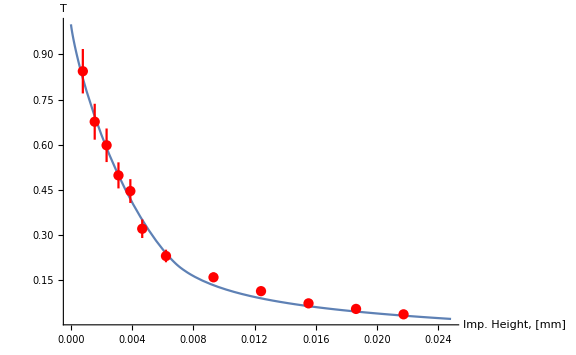

```mathematica
Needs["ErrorBarPlots`"]
Show[
Plot[Re[NIntegrate[f[h[x,y,10r(1-Cos[2/3θ0])]]/f[0]/20/r/(1-Cos[2/3θ0]),{x,-10r(1-Cos[2/3θ0]),10r(1-Cos[2/3θ0])}]],{y,0,8r(1-Cos[2/3θ0])}],
ErrorListPlot[MapThread[{{#1 r(1-Cos[2/3θ0]),N[Length[Select[#2,Abs[#[[1]]]<10r(1-Cos[2/3θ0])&]]/A0[#2,10r(1-Cos[2/3θ0])]]},ErrorBar[N[Length[Select[#2,Abs[#[[1]]]<10r(1-Cos[2/3θ0])&]]/A0[#2,10r(1-Cos[2/3θ0])]^2 dA0[#2,10r(1-Cos[2/3θ0])]]]}&,{mimph,mres}],PlotStyle->Red]
,PlotRange->All,AxesOrigin->{0,0},ImageSize->Large,AxesLabel->{"Imp. Height, [mm]","T"}]
```

```mathematica
res13=DetData@TraceImport["28 Mar 2018 15"];(*α = -0.2°*)
res14=DetData@TraceImport["29 Mar 2018 11"];(*α = -0.4°*)
res15=DetData@TraceImport["30 Mar 2018 11"];(*α = -0.6°*)
res16=DetData@TraceImport["31 Mar 2018 12"];(*α = 0.2°*)
res17=<<"detector results/DET_N10^8SPH";
```

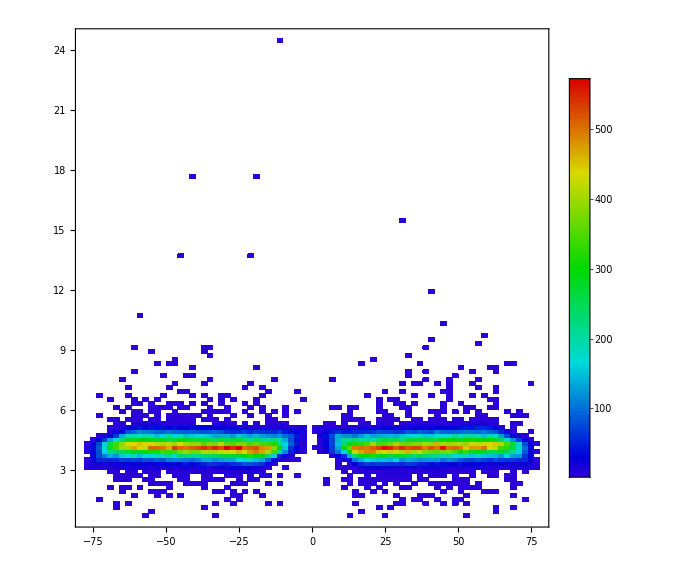

```mathematica
DensityHistogram[res14,100,ChartLegends->Automatic,ColorFunction->(Hue[0.7(1-#),1,0.85]&),ImageSize->Large]
```